```mathematica
SetOptions[$FrontEnd,DynamicEvaluationTimeout->Infinity]
```

# Quadratic Gravity And Scalar Dark Matter In A Gravitational Wave Context.

## Hontas Farmer and Shane Larson

We present, in the form of an interactive Mathematica notebook, a model of classical quadratic gravity with a massive scalar field in the context of extreme mass ratio in spirals which could be tested with the future Laser Interferometer Space Antenna.  The Lagrangian is written, field equations derived, then solved exactly without approximation.  Further computational investigation and evaluation was done to evaluate the consistency of the result with LIGO observations.  The result is a model which does not disturb the classic solar system test of general relativity but which in extreme conditions models cosmological behavior, and which would have LISA observable consequences in the context of an extreme mass ratio in spiral. Quadratic gravity theories are some of the best candidates for alternative gravity models which have not been eliminated by LIGO observation.  For example Starobinsky gravity, an inflationary model that fits available Planck data, while in the study of quantum gravity quadratic terms lead to a renormalization model. Given that data two parameters that appear in this model are precisely constrained to small but non-zero values.   Investigation of the EMRI environment may result in this model being validated or refuted by experiment as this paper shows.  

This Mathematica notebook is meant as a supplement to formal publication.  It includes details which are not appropriate for, or not possible in, the format of a journal paper.  For example some of the Mathematica code and results, if fully expanded make this document a few times longer, and there are interactive plots.

## Introduction

Quadratic gravity theories are some of the best candidates for alternative gravity models which have not been eliminated by LIGO observation.  For example Starobinsky gravity, an inflationary model that fits available Planck data, while in the study of quantum gravity quadratic terms lead to a renormalization model. For those reasons these models are very important and of great observational and theoretical interest.  

The model examined in this notebook is a combination of quadratic gravity found in literature as Starobinsky inflation1-2 with scalar field dark matter such as Fuzzy dark matter or axion dark matter very light scalar bosons 3-4.  This takes the form of an F(R) gravity model.  The goal is to build a straight forward understanding of these models and to probe if and how LISA will test them.

These models have been investigated theoretically for static situations and application to cosmology or in the context of quantum field theory in curved space time.   With the common assumption that the Ricci scalar would take on a small but non zero constant value 5 .  Gravitational wave physics presents a unique challenge where the Ricci scalar is not zero or any other constant.   While the space times of Black holes are of zero curvature the gravitational wave foreground that results from an in spiral of one black hole to another is not zero.  Solutions to these situations have been achieved by way of various computational and approximations methods such as parameterized post Newtonian, parameterized post Einsteinian 6, and EMRI Kluges 7.    These methods have all given good useful and computationally efficient results.  

 To definitively determine the physics beyond all reasonable doubt, I seek an exact mathematical model.  In this day computational perturbative solutions are often thought of as enough, but if exact solutions could be found why not try and find them? Having them will allow better use of computational power.

-Graphics-

The action which we will study is as follows.

S=∫√-g[f(R)-1/2 g^μν∇_μ ϕ∇_ν ϕ-1/2 mϕ^2]ⅆ^4 x

In which f(R) is given as the following.

f(R)=R+βR^2-ξRϕ^2

### Deriving the field equations

Deriving the field equations due to this action is a matter of taking functional/variational derivatives 8. The immediate result of this process will be modified Einstein field equations, and also a modified equation for a scalar field in curved space time with a Starobinsky term.  As demonstrated in CQ Geng how this will look given a particular f(R) is 

Many people who study gravitational waves in the observational sense tend to ignore the fact that gravitational waves have a non zero Ricci curvature even though the background space time has zero curvature.   Anyone who objects to this fact can read Sean Carolls textbook and write him an angry letter.

f'(R)R_μν-1/2 f(R)g_μν+(g_μν-∇_μ ∇_ν)f'(R)=κ^2 T_μν

This can then be traced as shown in CQ Geng into a form which is only in terms of invariants

f'(R)R-2f(R)+3□ f'(R)=κ^2 T

For the f(R) we are studying in this paper take a derivative with respect to R (d/dR as if it was X and this was a 1 D problem.  Strange as that may feel since we know R is itself a function of four space time variables.  That is the simple beauty of working with invariants.) Carrying out this problem as much as possible using the faultless math of Mathematica.

(6 β□- 1+ξ ϕ^2)R-3 ξ □ϕ^2 =κ^2 T

The process of taking the functional derivative of the action for the scalar field phi leads to the field equation for that field.  The result is a set of two field equations which will need to be solved simultaneously to fully solve the problem.

{ (□- 1/(6 β)+ξ/(6 β) ϕ^2)R-ξ/(2β) □ϕ^2 =κ^2/(6 β)T
(□-m^2-ξ R)ϕ=0}

A solution to the above set of equations should not depend on the choice of coordinates. The problem as it stands is formulated in terms of invariant quantities and the solutions should themselves be invariants. When coordinates are chosen, and the correct limits are taken the amplitude of the fields should drop off as 1/r or 1/r^2 .

## Solving the field equations up to an integral, analytically.

To solve these analytically let us consider some extremal cases.  Then using this simplified cases we can assemble an analytical solution.

### Setting the Starobinsky coefficient to zero, β =0

This is not allowed due to the appearance of terms which contain beta in the denominator.

{ (□- 1/(6 0)+ξ/(6 0) ϕ^2)R-ξ/(2 0) □ϕ^2 =κ^2/(6 0)T
(□-m^2-ξ R)ϕ=0}

This would lead to expressions that are undefined mathematically.

### Setting the Ricci scalar to zero, R =0 Case1

Setting R equal to zero causes the field equations to collapse to a simple form.

{ -ξ/(2β) □ϕ^2 =κ^2/(6 β)T
(□-m^2)ϕ=0}

This form of the equations is Ricci vacuum.  The result is that ϕ is described by the Klein-Gordon equation in flat space time.

(□-m^2)ϕ=0

Following the methods of Caroll and basic calculus.  The equation can be simplified by transforming it into a first order equation using an appropriate Killing vector.  Once this is done we get two complex valued equations one for the positive energy states and one for the negative energy states.  The solutions to these give us exponentials which lead to wave functions.   The solution works out to

ϕ=ϕ_0 e^(-ⅈω∫k_μ ⅆ x^μ)+ϕ_1 e^(ⅈω∫k_μ ⅆ x^μ)

In which k_μ is an appropriately chosen Killing vector.

There is a small modification to the stress energy invariant in this case.

T=- (3ξ)/κ^2□ϕ^2

### Setting the Starobinsky coefficient to zero, ϕ =0 Case2

In this case the scalar field does not exist the result is an equation which can be solved by the same methods as used for the Klein-Gordon equation in curved space time.

(□- 1/(6 β))R =κ^2/(6 β)T

The procedure and result are very similar. The difference is there is a recursive term that appears where in the value at one point depends on the value previously.

g_i =e^(-ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i √((κ^2 T)/(6 β))ⅆ x^μ)

g_i^*=e^(ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i √((κ^2 T)/(6 β))ⅆ x^μ)

The solution is then.

R=R_0 e^(-ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i √((κ^2 T)/(6 β))ⅆ x^μ)+R_1 e^(ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i^*√((κ^2 T)/(6 β))ⅆ x^μ)

### Setting the Starobinsky coefficient to zero, ξ =0 Case 3

In this case the equations are decoupled with no explicit interaction between the fields in the field equations.

{ (□- 1/(6 β))R =κ^2/(6 β)T
(□-m^2)ϕ=0}

The solutions to the two cases above apply to this case.

ϕ=ϕ_0 e^(-ⅈω∫k_μ ⅆ x^μ)+ϕ_1 e^(ⅈω∫k_μ ⅆ x^μ)

R=R_0 e^(-ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i √((κ^2 T)/(6 β))ⅆ x^μ)+R_1 e^(ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i^*√((κ^2 T)/(6 β))ⅆ x^μ)

### The General Solution

{ (□- 1/(6 β)+ξ/(6 β) ϕ^2)R-ξ/(2β) □ϕ^2 =κ^2/(6 β)T
(□-m^2-ξ R)ϕ=0}

With the insight gained from the special cases the general solution can be written by combining these solutions. Furthermore as the computer algebra system points out in the section below an arbitrary function must be inserted to match the boundary condition at infinity.

```mathematica
1/(4 π^2 σ(Subscript[x, 1],Subscript[x, 2]))
```

In which σ(x_1,x_2) is at simplest the interval between two points in the curved space time.   

The general solution with the boundary condition that it goes to zero at infinity is given by.

ϕ=1/(4 π^2 σ(x_1,x_2))(ϕ_0 e^(∫k_μ(-ⅈω+ξR)ⅆ x^μ)+ϕ_1 e^(∫k_μ(ⅈω+ξR)ⅆ x^μ))

R=1/(4 π^2 σ(x_1,x_2))(R_0 e^(∫k_μ(-ⅈω- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ)+R_1 e^(∫k_μ(ⅈω- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ))

### Computer Assisted Evaluation Of Integrals.

The solution for the field equations found by the analytical method above contains a set of integrals that while doable would be tedious with many steps.   In particular ∫k_μ ⅆ x^μ  and ∫K_μ(ⅈ ω+ξ R)ⅆ x^μ etc.

R=1/(4 π^2 σ(x_1,x_2))(R_0 Exp[-ⅈ ω ∫k_μ ⅆ x^μ]+R_1 Exp[ⅈ ω ∫k_μ ⅆ x^μ])

ϕ=1/(4 π^2 σ(x_1,x_2))(ϕ_0 Exp[∫K_μ(- ⅈ ω+ξ R)ⅆ x^μ ]+ϕ_1 Exp[∫K_μ(ⅈ ω+ξ R)ⅆ x^μ ])

The above equations have the virtues of being stated in terms of invariants and in coordinate free form.  Thus they satisfy all the requirements of General Relativity.  The computer algebra system Mathematica does not care about this important fact.  To encode this into the math we must choose a coordinate system and specify the normalized helical killing vector  K_μ in it.  Naturally the problem has spherical symmetry so spherical coordinates` are used.

```mathematica
Subscript[k, μ]={(-(1-(2 G M)/r)),0,0,Ω r^2 (Sin[θ])^2}
```

```mathematica
k^μ={1,0,0,Ω}
```

```mathematica
Subscript[K, μ]=Subscript[k, μ]/(k^μ Subscript[k, μ])
```

```mathematica
({(-(1-(2 G M)/r)),0,0,Ω r^2 (Sin[θ])^2}/({1,0,0,Ω}.{(-(1-(2 G M)/r)),0,0,Ω r^2 (Sin[θ])^2})).{dt,dr,dθ,dϕ}
```

Now to take the indicated integrals∫K_μ ⅆ x^μ

```mathematica
∫(-1+(2 G M)/r)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆϕ//FullSimplify
```

To complete the solution we need the metric tensor to use it to write down the relativistic separation between the points.

g^μν=(-(1-(2G M)/r) | 0 | 0 | 0
0 | (1-(2G M)/r)^-1 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin^2 θ )

For the computer.

```mathematica
g=({{-(1-(2G M)/r), 0, 0, 0}, {0, (1-(2G M)/r)^-1, 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2(Sin[θ])^2}})
```

```mathematica
σ= g .{t,r,θ,ϕ}.{t,r,θ,ϕ}
```

Now we can write the full solution

```mathematica
1/(4 π^2 σ)(R0 Exp[-ⅈ ω(∫(-1+(2 G M)/r)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆϕ) ]+R1 Exp[ⅈ ω(∫(-1+(2 G M)/r)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆϕ) ])//FullSimplify
```

```mathematica
Ricci=(ⅇ^(-(ⅈ ω (2 G M t-r t+r^3 ϕ Ω Sin[θ]^2))/(2 G M-r+r^3 Ω^2 Sin[θ]^2)) (2 G M-r) r (R0+ⅇ^((2 ⅈ ω (2 G M t-r t+r^3 ϕ Ω Sin[θ]^2))/(2 G M-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (4 G^2 M^2 t^2+r (-4 G M t^2+r (t^2-r (r+(-2 G M+r) θ^2)))+(2 G M-r) r^3 ϕ^2 Sin[θ]^2))
```

Now for the scalar field.

```mathematica
1/(4 π^2 σ)(ϕ0 Exp[-ⅈ ω(∫(-1+(2 G M)/r)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆϕ) +ξ Ricci]+ϕ1 Exp[ⅈ ω(∫(-1+(2 G M)/r)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆϕ)+ξ Ricci ])
```

```mathematica
Phifield=(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1)/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2))
```

Now we need to check the limits at the origin and at infinity.  This needs to be finite at both.

```mathematica
Limit[{Ricci,Phifield}, r->0]//FullSimplify
```

{0,0}

```mathematica
Limit[{Ricci,Phifield}, r->∞]//FullSimplify
```

{0,0}

This shows the gravitational wave Ricci goes to a constant the value of which will shrink as the amplitude of the EMRI orbit increases.   Meanwhile the same is for Phifield.   The boundary at infinity and the initial values being satisfied the solution for this system of equations, in Schwarzschild space time can be written as follows.

```mathematica
Ricci//TraditionalForm
```

(r (2 G M-r) exp(-(ⅈ ω (2 G M t+r^3 Ω ϕ sin^2(θ)-r t))/(2 G M+r^3 Ω^2 sin^2(θ)-r)) (R0+R1 exp((2 ⅈ ω (2 G M t+r^3 Ω ϕ sin^2(θ)-r t))/(2 G M+r^3 Ω^2 sin^2(θ)-r))))/(4 π^2 (4 G^2 M^2 t^2+r^3 ϕ^2 sin^2(θ) (2 G M-r)+r (r (t^2-r (θ^2 (r-2 G M)+r))-4 G M t^2)))

```mathematica
((8 π^2-r) r exp(-(ⅈ ω (r^3 Ω ϕ sin^2(θ)-r t+8 π^2 t))/(r^3 Ω^2 sin^2(θ)-r+8 π^2)) (R0+R1 exp((2 ⅈ ω (r^3 Ω ϕ sin^2(θ)-r t+8 π^2 t))/(r^3 Ω^2 sin^2(θ)-r+8 π^2))))/(4 π^2 ((8 π^2-r) r^3 ϕ^2 sin^2(θ)+r (r (t^2-r (θ^2 (r-8 π^2)+r))-16 π^2 t^2)+64 π^4 t^2))
```

```mathematica
Phifield//TraditionalForm
```

1/(4 π^2 (θ^2 r^2+r^2 ϕ^2 sin^2(θ)+r^2/(1-(8 π^2)/r)+((8 π^2)/r-1) t^2))(ϕ0 exp((ξ (8 π^2-r) r exp(-(ⅈ ω (r^3 Ω ϕ sin^2(θ)-r t+8 π^2 t))/(r^3 Ω^2 sin^2(θ)-r+8 π^2)) (R0+R1 exp((2 ⅈ ω (r^3 Ω ϕ sin^2(θ)-r t+8 π^2 t))/(r^3 Ω^2 sin^2(θ)-r+8 π^2))))/(4 π^2 ((8 π^2-r) r^3 ϕ^2 sin^2(θ)+r (r (t^2-r (θ^2 (r-8 π^2)+r))-16 π^2 t^2)+64 π^4 t^2))-ⅈ ω ((r^2 Ω ϕ sin^2(θ))/(r^2 Ω^2 sin^2(θ)+(8 π^2)/r-1)+(8 π^2 t)/(r (r^2 Ω^2 sin^2(θ)+(8 π^2)/r-1))-t/(r^2 Ω^2 sin^2(θ)+(8 π^2)/r-1)))+ϕ1 exp((ξ (8 π^2-r) r exp(-(ⅈ ω (r^3 Ω ϕ sin^2(θ)-r t+8 π^2 t))/(r^3 Ω^2 sin^2(θ)-r+8 π^2)) (R0+R1 exp((2 ⅈ ω (r^3 Ω ϕ sin^2(θ)-r t+8 π^2 t))/(r^3 Ω^2 sin^2(θ)-r+8 π^2))))/(4 π^2 ((8 π^2-r) r^3 ϕ^2 sin^2(θ)+r (r (t^2-r (θ^2 (r-8 π^2)+r))-16 π^2 t^2)+64 π^4 t^2))+ⅈ ω ((r^2 Ω ϕ sin^2(θ))/(r^2 Ω^2 sin^2(θ)+(8 π^2)/r-1)+(8 π^2 t)/(r (r^2 Ω^2 sin^2(θ)+(8 π^2)/r-1))-t/(r^2 Ω^2 sin^2(θ)+(8 π^2)/r-1))))

### Computer Algebra Solution

To be certain the above math is  correct we now demonstrate a solution which is found via the Mathematica computer algebra system.  It is as simple as putting the derivatives and killing vectors etc into a form which Mathematica can interpret and simplify by hand.   I will also leave the gravitational wave arbitrary.  The result will give a solution up to an integral. 

For simplicity the dependence of R on ϕ^2 will be ignored as it is presumed ϕ is small.

(□- 1/(6 β)+ξ/(6 β) ϕ^2)R-ξ/(2β) □ϕ^2 =κ^2/(6 β)T

```mathematica
DSolve[{D[u[t,r,θ,ϕ],t]+Ω/(r Sin[θ]) D[u[t,r,θ,ϕ],ϕ]==(-ⅈ ω+1/(6 β))u[t,r,θ,ϕ]},u[t,r,θ,ϕ],{t,r,θ,ϕ}]
```

```mathematica
DSolve[{D[u[t,r,θ,ϕ],t]+Ω/(r Sin[θ]) D[u[t,r,θ,ϕ],ϕ]==(ⅈ ω+1/(6 β))u[t,r,θ,ϕ]},u[t,r,θ,ϕ],{t,r,θ,ϕ}]
```

The solutions that the computer finds  is similar to that found by hand up to an integral over the Ricci scalar with a arbitrary function of r,θ and ϕ.  The simplest function that can satisfy the boundary conditions at infinity, and be compatible with theoretical expectation  is almost given in the solution.  We will modify it a bit to ensure that it stays finite at all values of the variables.   

(r ϕ-t Ω Csc[θ]θ)/r^2

```mathematica
Rcas=(ⅇ^(1/6 t (1/β-6 ⅈ ω)) (R0+ⅇ^(2 ⅈ t ω) R1) (r ϕ-t θ Ω Csc[θ]))/r^2
```

Now to Solve for ϕ ...

```mathematica
DSolve[{D[f[t,r,θ,ϕ],t]+Ω/(r Sin[θ]) D[f[t,r,θ,ϕ],ϕ]==(-ⅈ ω+ξ ((ⅇ^(1/6 t (1/β-6 ⅈ ω)) (R0+ⅇ^(2 ⅈ t ω) R1) (r ϕ-t θ Ω Csc[θ]))/r^2))f[t,r,θ,ϕ]},f[t,r,θ,ϕ],{t,r,θ,ϕ}]
```

```mathematica
DSolve[{D[f[t,r,θ,ϕ],t]+Ω/(r Sin[θ]) D[f[t,r,θ,ϕ],ϕ]==(ⅈ ω+ξ ((ⅇ^(1/6 t (1/β-6 ⅈ ω)) (R0+ⅇ^(2 ⅈ t ω) R1) (r ϕ-t θ Ω Csc[θ]))/r^2))f[t,r,θ,ϕ]},f[t,r,θ,ϕ],{t,r,θ,ϕ}]
```

With these findings the computer algebra solutions can be written down

R=(ⅇ^(1/6 t (1/β-6 ⅈ ω)) (R0+ⅇ^(2 ⅈ t ω) R1) (r ϕ-t θ Ω Csc[θ]))/r^2

ϕ=(r ϕ-t Ω Csc[θ]θ)/r^2(ϕ0 ⅇ^(-ⅈ t ω-(6 ⅇ^(1/6 t (1/β-6 ⅈ ω)) β (-1+θ) ξ ((ⅇ^(2 ⅈ t ω) R1 (6 β+t (-1-6 ⅈ β ω)))/(ⅈ-6 β ω)^2+(R0 (6 β+t (-1+6 ⅈ β ω)))/(ⅈ+6 β ω)^2) Ω Csc[θ])/r^2+(6 ⅇ^(1/6 t (1/β-6 ⅈ ω)) β ξ (R0+6 ⅈ R0 β ω+ⅇ^(2 ⅈ t ω) R1 (1-6 ⅈ β ω)) (r ϕ-t Ω Csc[θ]))/(r^2 (1+36 β^2 ω^2))) + ϕ1 ⅇ^(ⅈ t ω-(6 ⅇ^(1/6 t (1/β-6 ⅈ ω)) β (-1+θ) ξ ((ⅇ^(2 ⅈ t ω) R1 (6 β+t (-1-6 ⅈ β ω)))/(ⅈ-6 β ω)^2+(R0 (6 β+t (-1+6 ⅈ β ω)))/(ⅈ+6 β ω)^2) Ω Csc[θ])/r^2+(6 ⅇ^(1/6 t (1/β-6 ⅈ ω)) β ξ (R0+6 ⅈ R0 β ω+ⅇ^(2 ⅈ t ω) R1 (1-6 ⅈ β ω)) (r ϕ-t Ω Csc[θ]))/(r^2 (1+36 β^2 ω^2))))

This set of equations matches the major features of the solution found above and differs only in the simplifying assumptions needed to make the math doable by Mathematica.   This gives me confidence that the math was done correctly by hand.

### Plotting The Fields

For plotting we need the constants of nature for our plots.  For this a choice of units must be made.  Given that the systems we are going to study are of broadly solar system scale the unit of time will be years, the unit of distance will be astronomical units and the unit of mass will be solar masses.   This choice also facilitates computation by keeping the numbers manageable for any reasonable desktop computer.   The ranges of values available are chosen to be certain that the graphs produced will show the important features. In this system of units the gravitational constant G will be given by

```mathematica
G=4 π^2 M^-1
```

(4 π^2)/M

The speed of light will be 63198 au/yr

```mathematica
c=63198
```

63198

A constant κ appears multiple times in the equations it must also be defined.

```mathematica
κ=(8π G)/c^4
```

(2 π^3)/(996995861607233601 M)

A crucial consideration is the range of frequencies that it would even be reasonable to consider.  Mathematically any arbitrary frequency can be input.  Physically certain frequencies will result in physically impossible situations.

-Graphics-

This sensitivity curve was consulted to choose the reasonable range of frequencies that could be realistically detected by LISA.  (Amaro-Seoane et al. 2017)9

The range of frequencies will be from 320 cycles pear year to 320000 cycles per year.   Upon careful consideration of all the factors the parameters used in all of these plots vary over the following ranges.

```mathematica
Ricci
```

```mathematica
Manipulate[Plot[Re[(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))],{t,-100/63241,3.12*^-9},PlotPoints->1000,AxesLabel->{"Time (yrs)","Amplitude(AU^-2)"}],{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5}]
```

Now to plot the scalar field including it’s interaction with the gravitational field.  (In the following graphs to replicate the graphs which appear in the paper set ξ = 6.22969*^-20 and β =1/5000000000.  There was no apriori reason for these numbers they happen to give graphs that are most pleasing aesthetically and scientifically).

```mathematica
Phifield
```

```mathematica
Manipulate[Plot[Re[(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1)/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2))],{t,-100/63241,3.12*^-9},PlotPoints->1000,AxesLabel->{"Time (yrs)","Amplitude(AU^-2)"}],{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6}]
```

Take note of what the vertical axis does as you move the slider increasing the radial distance r.   This shows that the inverse square law is being obeyed. 

The following analyses will be done based on the solutions found by hand.

### Tensor Analysis

Following with the textbook and in reference to CQ Gengs work using equation 7.7 in Caroll I was able to solve  for the metric of the gravitational wave in terms of the Ricci curvature itself.

R=∂_μ ∂_ν h^μν-□h

We will also use the trace reverse perturbation as shown in the book.

(h̄)^μν=h^μν-h η^μν

We will also work under the Lorenz gauge condition.

∂_μ h^μν=0

Using this gauge condition, substituting into equation 15 and simplifying results in the next equation.

R=-3 η^μν□h_μν

To solve this equation for h_μν the steps are to multiply both sides by negative one third and η_μν.  Then divide both sides by η_μν η^μν.  Then integrate both sides twice. Using the fact that for the Minkowski metric integrating will have a different variable than that which appears in the metric so it can be moved outside of the integrals.  Thus a general solution to this equation, in Lorenz gauge, can be written down.

h^μν=-1/3 η^μν/(η_μν η^μν)∫∫Rⅆ x_μⅆ x^μ

To simplify equation 16 requires integration by parts then dropping terms that contain a derivative of the scalar field.  So Ricci modified will be.

R_modified=1/(4 π^2 σ(x_1,x_2))(R_0 e^((-ⅈω- ξ/(6 β)ϕ^2[R])∫k_μ ⅆ x^μ)+R_1 e^((ⅈω- ξ/(6 β)ϕ^2[R])∫k_μ ⅆ x^μ))

The following form allows for evaluating equation 16 more easily.

R_modified=1/(4 π^2 σ(x_1,x_2))(R_0 e^(-ⅈω∫k_μ ⅆ x^μ)+R_1 e^(ⅈω∫k_μ ⅆ x^μ))e^(- ξ/(6 β)ϕ^2[R]∫k_μ ⅆ x^μ)

Carrying out integration by parts again, and dropping terms that have the derivative of the scalar field ϕ.  In equations 18 and 19 R is the unmodified scalar.

h^μν=-1/3 η^μν/(η_μν η^μν)e^(- ξ/(6 β)ϕ^2[R]∫k_μ ⅆ x^μ)∫∫Rⅆ x_μⅆ x^μ

Finding the strain scalar means multiplying by the Minkowski metric one more time.

h=-1/3 e^(- ξ/(6 β)ϕ^2[R]∫k_μ ⅆ x^μ)∫∫Rⅆ x_μⅆ x^μ

Working this out in Mathematica and noting that the metric isn’t totally gone. ⅆ x_μⅆ x^μ =ⅆ x_μ η^μν ⅆ x_ν

```mathematica
∫ Ricciⅆr
```

Expanding this with series so the undoable integrals can be done.  This is at the cost of exact precision. .

```mathematica
Series[Ricci,{r,0,4}]//FullSimplify
```

```mathematica
Riccirseries=(ⅇ^(-ⅈ t ω) (R0+ⅇ^(2 ⅈ t ω) R1) r)/(32 π^4 t^2)+(ⅇ^(-ⅈ t ω) (R0+ⅇ^(2 ⅈ t ω) R1) r^2)/(256 π^6 t^2)+(ⅇ^(-ⅈ t ω) (R0+ⅇ^(2 ⅈ t ω) R1) r^3)/(2048 π^8 t^2)+1/(16384 π^10 t^4)ⅇ^(-ⅈ t ω) ((R0+ⅇ^(2 ⅈ t ω) R1) (t^2-64 π^4 θ^2)-64 π^4 (R0 (ϕ^2+ⅈ t^2 ϕ ω Ω-ⅈ t^3 ω Ω^2)+ⅇ^(2 ⅈ t ω) R1 (ϕ^2-ⅈ t^2 ϕ ω Ω+ⅈ t^3 ω Ω^2)) Sin[θ]^2) r^4
```

```mathematica
Riccirseries
```

```mathematica
Series[Ricci,{θ,0,4}]//FullSimplify
```

```mathematica
Riccithetaseries=(ⅇ^(-ⅈ t ω) (8 π^2-r) r (R0+ⅇ^(2 ⅈ t ω) R1))/(4 π^2 (-r^4+(-8 π^2+r)^2 t^2))+(ⅇ^(-ⅈ t ω) r^4 (-(-8 π^2+r)^2 (R0+ⅇ^(2 ⅈ t ω) R1) (1+ϕ^2)+ⅈ (R0-ⅇ^(2 ⅈ t ω) R1) (r^4-(-8 π^2+r)^2 t^2) ω Ω (ϕ-t Ω)) θ^2)/(4 π^2 (r^4-(-8 π^2+r)^2 t^2)^2)+1/(24 π^2)ⅇ^(-ⅈ t ω) (8 π^2-r) r^4 ((2 (8 π^2-r) (R0+ⅇ^(2 ⅈ t ω) R1) (3 (8 π^2-r) r^3+((48 π^2-7 r) r^3+(-8 π^2+r)^2 t^2) ϕ^2+3 (8 π^2-r) r^3 ϕ^4))/(-r^4+(-8 π^2+r)^2 t^2)^3+(6 ⅈ r^3 (R0-ⅇ^(2 ⅈ t ω) R1) (1+ϕ^2) ω Ω (ϕ-t Ω))/((r^4-(-8 π^2+r)^2 t^2)^2)+(ω Ω (-ϕ+t Ω) (ⅇ^(2 ⅈ t ω) R1 (16 ⅈ π^2-2 ⅈ r+3 r^3 Ω (ϕ ω+2 ⅈ Ω-t ω Ω))+R0 (-16 ⅈ π^2+2 ⅈ r-3 r^3 Ω (-ϕ ω+2 ⅈ Ω+t ω Ω))))/(-r^4 (-8 π^2+r)^2+(-8 π^2+r)^4 t^2)) θ^4
```

```mathematica
Riccithetaseries
```

Now this integral can be done.

```mathematica
-1/3 Exp[-ξ/(6β)(Phifield)^2(8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)](∫(∫-Ricciⅆt)ⅆt+∫(∫ Riccirseriesⅆr)ⅆr+∫(∫Riccithetaseries/r^2 ⅆθ)ⅆθ+∫(∫Ricci/(Sin[θ])^2 ⅆϕ)ⅆϕ)
```

```mathematica
hscalar=-1/3 ⅇ^(-(ξ (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1)^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(96 π^4 β (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))) ((ⅇ^(-ⅈ t ω) r^3 R0)/(192 π^4 t^2)+(ⅇ^(-ⅈ t ω) r^4 R0)/(3072 π^6 t^2)+(ⅇ^(-ⅈ t ω) r^5 R0)/(40960 π^8 t^2)+(ⅇ^(ⅈ t ω) r^3 R1)/(192 π^4 t^2)+(ⅇ^(ⅈ t ω) r^4 R1)/(3072 π^6 t^2)+(ⅇ^(ⅈ t ω) r^5 R1)/(40960 π^8 t^2)+(ⅇ^(-ⅈ t ω) r^6 (R0+ⅇ^(2 ⅈ t ω) R1) (t^2-64 π^4 θ^2))/(491520 π^10 t^4)+1/(24 π^2 r)ⅇ^(-ⅈ t ω) ((3 (8 π^2-r) (R0+ⅇ^(2 ⅈ t ω) R1) θ^2)/(-r^4+(-8 π^2+r)^2 t^2)+(r^3 θ^4 (-(-8 π^2+r)^2 (R0+ⅇ^(2 ⅈ t ω) R1) (1+ϕ^2)+ⅈ (R0-ⅇ^(2 ⅈ t ω) R1) (r^4-(-8 π^2+r)^2 t^2) ω Ω (ϕ-t Ω)))/(2 (r^4-(-8 π^2+r)^2 t^2)^2)+1/30 (8 π^2-r) r^3 θ^6 ((2 (8 π^2-r) (R0+ⅇ^(2 ⅈ t ω) R1) (3 (8 π^2-r) r^3+((48 π^2-7 r) r^3+(-8 π^2+r)^2 t^2) ϕ^2+3 (8 π^2-r) r^3 ϕ^4))/(-r^4+(-8 π^2+r)^2 t^2)^3+(6 ⅈ r^3 (R0-ⅇ^(2 ⅈ t ω) R1) (1+ϕ^2) ω Ω (ϕ-t Ω))/((r^4-(-8 π^2+r)^2 t^2)^2)+(ω Ω (-ϕ+t Ω) (ⅇ^(2 ⅈ t ω) R1 (16 ⅈ π^2-2 ⅈ r+3 r^3 Ω (ϕ ω+(2 ⅈ-t ω) Ω))+R0 (-16 ⅈ π^2+2 ⅈ r-3 r^3 Ω (-ϕ ω+(2 ⅈ+t ω) Ω))))/(-r^4 (-8 π^2+r)^2+(-8 π^2+r)^4 t^2)))-1/(4 π^2)(8 π^2-r) r ((ⅇ^(-(2 ⅈ √2 r^(3/2) (-8 π^2+r) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))+(ⅈ ω (√2 r^(3/2) (-8 π^2+r) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])+2 √((8 π^2-r)^2) r^3 ϕ Ω Sin[θ]^2))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))) R1 t ExpIntegralEi[-((ⅈ (8 π^2-r) ω (-2 √((8 π^2-r)^2) t+√2 r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])))])/(√2 √((8 π^2-r)^2) r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))+(ⅇ^(-(4 ⅈ √2 (8 π^2-r) r^(3/2) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^(3/2) (-8 π^2+r) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(ⅈ ω (√2 r^(3/2) (-8 π^2+r) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])+2 √((8 π^2-r)^2) r^3 ϕ Ω Sin[θ]^2))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))) R0 t ExpIntegralEi[(ⅈ (8 π^2-r) ω (-2 √((8 π^2-r)^2) t+√2 r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))])/(√2 √((8 π^2-r)^2) r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 (8 π^2-r) r^(3/2) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^(3/2) (-8 π^2+r) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(ⅈ ω (√2 r^(3/2) (-8 π^2+r) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])+2 √((8 π^2-r)^2) r^3 ϕ Ω Sin[θ]^2))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))) R0 t ExpIntegralEi[-((ⅈ (8 π^2-r) ω (2 √((8 π^2-r)^2) t+√2 r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])))])/(√2 √((8 π^2-r)^2) r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 (8 π^2-r) r^(3/2) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^(3/2) (-8 π^2+r) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))+(ⅈ ω (√2 r^(3/2) (-8 π^2+r) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])+2 √((8 π^2-r)^2) r^3 ϕ Ω Sin[θ]^2))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))) R1 t ExpIntegralEi[(ⅈ (8 π^2-r) ω (2 √((8 π^2-r)^2) t+√2 r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))])/(√2 √((8 π^2-r)^2) r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])))-1/(4 π^2)(8 π^2-r) r (-2 ⅇ^(-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])+(ⅈ r^3 ϕ ω Ω Cos[2 θ]^2)/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])-(ⅈ r^3 ϕ ω Ω Cos[4 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])-(2 r^3 ϕ ω Ω Cos[2 θ] Sin[2 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])-(ⅈ r^3 ϕ ω Ω Sin[2 θ]^2)/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])+(r^3 ϕ ω Ω Sin[4 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])) R0 (1/(4 (8 π^2-r)^2)ⅇ^((r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])))/(√2 √((8 π^2-r)^2))) ExpIntegralEi[t ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-1/(√2 √((8 π^2-r)^2))r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]+1/(4 (8 π^2-r)^2)ⅇ^(-(r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])))/(√2 √((8 π^2-r)^2))) ExpIntegralEi[t ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+1/(√2 √((8 π^2-r)^2))r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])-2 ⅇ^((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(ⅈ r^3 ϕ ω Ω Cos[2 θ]^2)/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])+(ⅈ r^3 ϕ ω Ω Cos[4 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])+(2 r^3 ϕ ω Ω Cos[2 θ] Sin[2 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])+(ⅈ r^3 ϕ ω Ω Sin[2 θ]^2)/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])-(r^3 ϕ ω Ω Sin[4 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])) R1 (1/(4 (8 π^2-r)^2)ⅇ^((r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) (-(16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])))/(√2 √((8 π^2-r)^2))) ExpIntegralEi[t (-(16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-1/(√2 √((8 π^2-r)^2))r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) (-(16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]+1/(4 (8 π^2-r)^2)ⅇ^(-(r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) (-(16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])))/(√2 √((8 π^2-r)^2))) ExpIntegralEi[t (-(16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+1/(√2 √((8 π^2-r)^2))r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) (-(16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]))-(ⅇ^(-ⅈ t ω) r^6 (R0 (ϕ^2+ⅈ t^2 ϕ ω Ω-ⅈ t^3 ω Ω^2)+ⅇ^(2 ⅈ t ω) R1 (ϕ^2-ⅈ t^2 ϕ ω Ω+ⅈ t^3 ω Ω^2)) Sin[θ]^2)/(7680 π^6 t^4)+(ⅇ^(-(ⅈ ω (r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) Ω-r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) Ω Cos[2 θ]+16 π^2 t √(-((8 π^2-r) r^3 Sin[θ]^2))-2 r t √(-((8 π^2-r) r^3 Sin[θ]^2))))/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) (8 π^2-r) r Csc[θ]^2 (-1/(2 r^3 ω Ω)ⅈ ⅇ^((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) R0 (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]) Csc[θ]^2+1/(2 r^3 ω Ω)ⅈ ⅇ^((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R0 (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]) Csc[θ]^2-1/(2 r^3 ω Ω)ⅈ ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) R1 (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]) Csc[θ]^2+1/(2 r^3 ω Ω)ⅈ ⅇ^((ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]))/((-8 π^2+r) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(4 ⅈ ω (r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) Ω Sin[θ]^2+(8 π^2-r) t √(-((8 π^2-r) r^3 Sin[θ]^2))))/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R1 (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]) Csc[θ]^2-R0 ϕ ExpIntegralEi[(2 ⅈ r^3 ω Ω (√2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2)-ϕ √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ])) Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))]+ⅇ^((4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R0 ϕ ExpIntegralEi[-((2 ⅈ r^3 ω Ω (√2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2)+ϕ √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ])) Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])))]+ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])) R1 ϕ ExpIntegralEi[(2 ⅈ r^3 ω Ω (√2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2)+ϕ √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ])) Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))]-ⅇ^((4 ⅈ ω (r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) Ω Sin[θ]^2+(8 π^2-r) t √(-((8 π^2-r) r^3 Sin[θ]^2))))/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R1 ϕ ExpIntegralEi[(2 ⅈ ω Ω (1/(√2)√(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ])+(8 π^2-r) r^3 ϕ Sin[θ]^2))/((8 π^2-r) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))]+1/(√2 r^3 (-8 π^2+r))ⅇ^(-(ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]))/((8 π^2-r) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))+(ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]))/((-8 π^2+r) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ ω (r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) Ω Sin[θ]^2+(8 π^2-r) t √(-((8 π^2-r) r^3 Sin[θ]^2))))/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R1 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) Csc[θ]^2 ExpIntegralEi[(ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]))/((8 π^2-r) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])]+√2 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) R1 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]+1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])+2 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^4 R1 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-128 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^4 R1 t^2 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+32 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^2 r R1 t^2 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-2 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^2 R1 t^2 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-16 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^2 r^3 R1 θ^2 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+2 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^4 R1 θ^2 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+√2 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) R0 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]+1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])+√2 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R0 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]+1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])-2 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^4 R0 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+2 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) r^4 R0 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+128 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^4 R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-128 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) π^4 R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-32 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^2 r R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+32 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) π^2 r R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+2 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^2 R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-2 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) r^2 R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+16 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^2 r^3 R0 θ^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-16 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) π^2 r^3 R0 θ^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-2 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^4 R0 θ^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+2 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) r^4 R0 θ^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))))/(8 π^2 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) √(-((8 π^2-r) r^3 Sin[θ]^2))))
```

The scalar field works out to the following.  The closed cells above this show the details of this computation.

```mathematica
hscalar
```

For completeness the full tensor is  found simply by application of the metric.

```mathematica
eta=({{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, (Sin[θ])^2}})
```

```mathematica
Tr[eta.eta]
```

2+r^4+Sin[θ]^4

Thus we get the full gravitational wave

```mathematica
eta/Tr[eta.eta] hscalar//MatrixForm
```

### Plots of h

So we will plot the scalar as it is easy to plot in 1d and is directly comparable to data.

```mathematica
Manipulate[Plot[Re[-1/3 ⅇ^(-(ξ (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1)^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(96 π^4 β (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))) ((ⅇ^(-ⅈ t ω) r^3 R0)/(192 π^4 t^2)+(ⅇ^(-ⅈ t ω) r^4 R0)/(3072 π^6 t^2)+(ⅇ^(-ⅈ t ω) r^5 R0)/(40960 π^8 t^2)+(ⅇ^(ⅈ t ω) r^3 R1)/(192 π^4 t^2)+(ⅇ^(ⅈ t ω) r^4 R1)/(3072 π^6 t^2)+(ⅇ^(ⅈ t ω) r^5 R1)/(40960 π^8 t^2)+(ⅇ^(-ⅈ t ω) r^6 (R0+ⅇ^(2 ⅈ t ω) R1) (t^2-64 π^4 θ^2))/(491520 π^10 t^4)+1/(24 π^2 r)ⅇ^(-ⅈ t ω) ((3 (8 π^2-r) (R0+ⅇ^(2 ⅈ t ω) R1) θ^2)/(-r^4+(-8 π^2+r)^2 t^2)+(r^3 θ^4 (-(-8 π^2+r)^2 (R0+ⅇ^(2 ⅈ t ω) R1) (1+ϕ^2)+ⅈ (R0-ⅇ^(2 ⅈ t ω) R1) (r^4-(-8 π^2+r)^2 t^2) ω Ω (ϕ-t Ω)))/(2 (r^4-(-8 π^2+r)^2 t^2)^2)+1/30 (8 π^2-r) r^3 θ^6 (1/((-r^4+(-8 π^2+r)^2 t^2)^3)2 (8 π^2-r) (R0+ⅇ^(2 ⅈ t ω) R1) (3 (8 π^2-r) r^3+((48 π^2-7 r) r^3+(-8 π^2+r)^2 t^2) ϕ^2+3 (8 π^2-r) r^3 ϕ^4)+(6 ⅈ r^3 (R0-ⅇ^(2 ⅈ t ω) R1) (1+ϕ^2) ω Ω (ϕ-t Ω))/(r^4-(-8 π^2+r)^2 t^2)^2+(ω Ω (-ϕ+t Ω) (ⅇ^(2 ⅈ t ω) R1 (16 ⅈ π^2-2 ⅈ r+3 r^3 Ω (ϕ ω+(2 ⅈ-t ω) Ω))+R0 (-16 ⅈ π^2+2 ⅈ r-3 r^3 Ω (-ϕ ω+(2 ⅈ+t ω) Ω))))/(-r^4 (-8 π^2+r)^2+(-8 π^2+r)^4 t^2)))-1/(4 π^2)(8 π^2-r) r ((ⅇ^(-(2 ⅈ √2 r^(3/2) (-8 π^2+r) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))+(ⅈ ω (√2 r^(3/2) (-8 π^2+r) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])+2 √((8 π^2-r)^2) r^3 ϕ Ω Sin[θ]^2))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))) R1 t ExpIntegralEi[-((ⅈ (8 π^2-r) ω (-2 √((8 π^2-r)^2) t+√2 r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])))])/(√2 √((8 π^2-r)^2) r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))+(ⅇ^(-(4 ⅈ √2 (8 π^2-r) r^(3/2) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^(3/2) (-8 π^2+r) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(ⅈ ω (√2 r^(3/2) (-8 π^2+r) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])+2 √((8 π^2-r)^2) r^3 ϕ Ω Sin[θ]^2))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))) R0 t ExpIntegralEi[(ⅈ (8 π^2-r) ω (-2 √((8 π^2-r)^2) t+√2 r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))])/(√2 √((8 π^2-r)^2) r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 (8 π^2-r) r^(3/2) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^(3/2) (-8 π^2+r) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(ⅈ ω (√2 r^(3/2) (-8 π^2+r) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])+2 √((8 π^2-r)^2) r^3 ϕ Ω Sin[θ]^2))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))) R0 t ExpIntegralEi[-((ⅈ (8 π^2-r) ω (2 √((8 π^2-r)^2) t+√2 r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])))])/(√2 √((8 π^2-r)^2) r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 (8 π^2-r) r^(3/2) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^(3/2) (-8 π^2+r) ω √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))+(ⅈ ω (√2 r^(3/2) (-8 π^2+r) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])+2 √((8 π^2-r)^2) r^3 ϕ Ω Sin[θ]^2))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))) R1 t ExpIntegralEi[(ⅈ (8 π^2-r) ω (2 √((8 π^2-r)^2) t+√2 r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])))/(√((8 π^2-r)^2) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))])/(√2 √((8 π^2-r)^2) r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ])))-1/(4 π^2)(8 π^2-r) r (-2 ⅇ^(-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])+(ⅈ r^3 ϕ ω Ω Cos[2 θ]^2)/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])-(ⅈ r^3 ϕ ω Ω Cos[4 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])-(2 r^3 ϕ ω Ω Cos[2 θ] Sin[2 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])-(ⅈ r^3 ϕ ω Ω Sin[2 θ]^2)/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])+(r^3 ϕ ω Ω Sin[4 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])) R0 (1/(4 (8 π^2-r)^2)ⅇ^((r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])))/(√2 √((8 π^2-r)^2))) ExpIntegralEi[t ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-1/(√2 √((8 π^2-r)^2))r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]+1/(4 (8 π^2-r)^2)ⅇ^(-(r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])))/(√2 √((8 π^2-r)^2))) ExpIntegralEi[t ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+1/(√2 √((8 π^2-r)^2))r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) ((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])-2 ⅇ^((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(ⅈ r^3 ϕ ω Ω Cos[2 θ]^2)/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])+(ⅈ r^3 ϕ ω Ω Cos[4 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])+(2 r^3 ϕ ω Ω Cos[2 θ] Sin[2 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])+(ⅈ r^3 ϕ ω Ω Sin[2 θ]^2)/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])-(r^3 ϕ ω Ω Sin[4 θ])/(r^3 Ω^2-32 π^2 Cos[2 θ]+4 r Cos[2 θ]-2 r^3 Ω^2 Cos[2 θ]+r^3 Ω^2 Cos[4 θ]-32 ⅈ π^2 Sin[2 θ]+4 ⅈ r Sin[2 θ]-2 ⅈ r^3 Ω^2 Sin[2 θ]+ⅈ r^3 Ω^2 Sin[4 θ])) R1 (1/(4 (8 π^2-r)^2)ⅇ^((r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) (-(16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])))/(√2 √((8 π^2-r)^2))) ExpIntegralEi[t (-((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-1/(√2 √((8 π^2-r)^2))r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) (-((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]+1/(4 (8 π^2-r)^2)ⅇ^(-(r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) (-(16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])))/(√2 √((8 π^2-r)^2))) ExpIntegralEi[t (-((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+1/(√2 √((8 π^2-r)^2))r^(3/2) √(2 r-16 π^2 θ^2+2 r θ^2-8 π^2 ϕ^2+r ϕ^2+8 π^2 ϕ^2 Cos[2 θ]-r ϕ^2 Cos[2 θ]) (-((16 ⅈ π^2 ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(2 ⅈ r ω)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]))-(ⅇ^(-ⅈ t ω) r^6 (R0 (ϕ^2+ⅈ t^2 ϕ ω Ω-ⅈ t^3 ω Ω^2)+ⅇ^(2 ⅈ t ω) R1 (ϕ^2-ⅈ t^2 ϕ ω Ω+ⅈ t^3 ω Ω^2)) Sin[θ]^2)/(7680 π^6 t^4)+(ⅇ^(-(ⅈ ω (r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) Ω-r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) Ω Cos[2 θ]+16 π^2 t √(-((8 π^2-r) r^3 Sin[θ]^2))-2 r t √(-((8 π^2-r) r^3 Sin[θ]^2))))/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) (8 π^2-r) r Csc[θ]^2 (-1/(2 r^3 ω Ω)ⅈ ⅇ^((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) R0 (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]) Csc[θ]^2+1/(2 r^3 ω Ω)ⅈ ⅇ^((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R0 (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]) Csc[θ]^2-1/(2 r^3 ω Ω)ⅈ ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) R1 (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]) Csc[θ]^2+1/(2 r^3 ω Ω)ⅈ ⅇ^((ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]))/((-8 π^2+r) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(4 ⅈ ω (r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) Ω Sin[θ]^2+(8 π^2-r) t √(-((8 π^2-r) r^3 Sin[θ]^2))))/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R1 (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]) Csc[θ]^2-R0 ϕ ExpIntegralEi[(2 ⅈ r^3 ω Ω (√2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2)-ϕ √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ])) Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))]+ⅇ^((4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R0 ϕ ExpIntegralEi[-((2 ⅈ r^3 ω Ω (√2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2)+ϕ √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ])) Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])))]+ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])) R1 ϕ ExpIntegralEi[(2 ⅈ r^3 ω Ω (√2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2)+ϕ √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ])) Sin[θ]^2)/(√(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))]-ⅇ^((4 ⅈ ω (r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) Ω Sin[θ]^2+(8 π^2-r) t √(-((8 π^2-r) r^3 Sin[θ]^2))))/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R1 ϕ ExpIntegralEi[(2 ⅈ ω Ω (1/(√2)√(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ])+(8 π^2-r) r^3 ϕ Sin[θ]^2))/((8 π^2-r) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))]+1/(√2 r^3 (-8 π^2+r))ⅇ^(-(ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]))/((8 π^2-r) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))+(ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]))/((-8 π^2+r) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ ω (r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) Ω Sin[θ]^2+(8 π^2-r) t √(-((8 π^2-r) r^3 Sin[θ]^2))))/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R1 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) Csc[θ]^2 ExpIntegralEi[(ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]))/((8 π^2-r) (16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]))-(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])]+√2 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) R1 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]+1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])+2 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^4 R1 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-128 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^4 R1 t^2 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+32 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^2 r R1 t^2 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-2 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^2 R1 t^2 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-16 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^2 r^3 R1 θ^2 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+2 ⅇ^((4 ⅈ (8 π^2-r) t ω)/(16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^4 R1 θ^2 (-((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[-((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+√2 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) R0 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]+1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])+√2 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) R0 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) (1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))]+1/(2 (8 π^2-r) r^3 (-1+Cos[2 θ]))ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])-2 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^4 R0 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+2 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) r^4 R0 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+128 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^4 R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-128 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) π^4 R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-32 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^2 r R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+32 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) π^2 r R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+2 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^2 R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-2 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) r^2 R0 t^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+16 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) π^2 r^3 R0 θ^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-16 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) π^2 r^3 R0 θ^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))-2 ⅇ^(-(2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) r^4 R0 θ^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))+2 ⅇ^((2 ⅈ √2 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω √((8 π^2-r) r^3 (-1+Cos[2 θ])) Sin[θ]^2)/((8 π^2-r) (-1+Cos[2 θ]) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))+(4 ⅈ r^3 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) ω Ω Sin[θ]^2)/((16 π^2-2 r+r^3 Ω^2-r^3 Ω^2 Cos[2 θ]) √(-((8 π^2-r) r^3 Sin[θ]^2)))) r^4 R0 θ^2 ((ⅇ^((2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ]))-(ⅇ^(-(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))) √(-8 π^2 r^3+r^4+8 π^2 r^3 Cos[2 θ]-r^4 Cos[2 θ]) ExpIntegralEi[(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ])+(2 ⅈ √2 r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) ω Ω Sin[θ]^2)/(√((8 π^2-r) r^3 (-1+Cos[2 θ])) (-16 π^2+2 r-r^3 Ω^2+r^3 Ω^2 Cos[2 θ]))])/(2 √2 (8 π^2-r) r^3 √(-r^4+64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 θ^2) (-1+Cos[2 θ])))))/(8 π^2 √(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)) √(-((8 π^2-r) r^3 Sin[θ]^2))))],{t,-100/63241,3.12*^-9},PlotPoints->200,AxesLabel->{"Time yrs","Metric Strain (h)"}],{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000}]
```

I do like how this compares to the available LIGO data at least in waveform and shape.

-Graphics-

We will also plot the percentage difference between the modified and unmodified theories.  Since the modifications to GR actually factor out this percentage difference takes on a simple form.

|e^(- ξ/(6 β)ϕ^2[R]∫k_μ ⅆ x^μ)-1|*100

```mathematica
Exp[-ξ/(6β)(Phifield)^2(8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)]-1
```

Plotting this percentage difference we get the following graph.

```mathematica
Manipulate[Plot[Re[Abs[-1+ⅇ^(-(ξ (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1)^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(96 π^4 β (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))]*100],{t,-100/63241,3.12*^-9},PlotPoints->200,AxesLabel->{"Time Years","Metric Strain (h)%diff"}],{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000}]
```

Now let us look at the percentage difference as a function of distance out to galactic cluster scale.

```mathematica
Manipulate[LogPlot[Re[Abs[-1+ⅇ^(-(ξ (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1)^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(96 π^4 β (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))]*100],{r,632410000000000,1.974*^-4},PlotPoints->200,AxesLabel->{"Distance AU","Metric Strain (h) %diff"}],{t,-10000000000,3.12*^-9},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,400000000}]
```

The percentage difference as a function of distance out to solar system scale.

```mathematica
Manipulate[LogPlot[Re[Abs[-1+ⅇ^(-(ξ (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1)^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(96 π^4 β (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))]*100],{r,.1,1.974*^-4},PlotPoints->200,AxesLabel->{"Distance AU","Metric Strain (h) %diff"}],{t,-0.1/63241,3.12*^-9},{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000}]
```

General::unfl: Underflow occurred in computation.

General::munfl: Exp[-1.56559×10^110+6.20414×10^110 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::unfl: Underflow occurred in computation.

1/5000000000

## Energy Considerations

Now that we have confidence in the solutions to the field equations, we will consider how the stress-energy invariant behaves in this model.   This invariant will be a physically observable quantity that is proportional to and will give the same wave form as the graphs of strain vs time which are standard in gravitational wave physics.

The stress energy invariant is found directly in the field equations with a bit of algebraic manipulation.

T=-1/κ^2R+(6 β)/κ^2□R+ξ/κ^2□ϕ+ξ/κ^2 ϕ^2 R

This was done because the general solutions, shown again below have a great deal of complication.  For R they contain terms that are quadratic in ϕ which itself depends on R and is linear in R.

ϕ=1/(4 π^2 σ(x_1,x_2))(ϕ_0 e^(∫k_μ(-ⅈω+ξR)ⅆ x^μ)+ϕ_1 e^(∫k_μ(ⅈω+ξR)ⅆ x^μ))

R=1/(4 π^2 σ(x_1,x_2))(R_0 e^(∫k_μ(-ⅈω- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ)+R_1 e^(∫k_μ(ⅈω- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ))

Initially these were simplified to the following form.

R=1/(4 π^2 σ(x_1,x_2))(R_0 Exp[-ⅈ ω ∫k_μ ⅆ x^μ]+R_1 Exp[ⅈ ω ∫k_μ ⅆ x^μ])

ϕ=1/(4 π^2 σ(x_1,x_2))(ϕ_0 Exp[- ⅈ ω∫K_μ ⅆ x^μ ]+ϕ_1 Exp[ⅈ ω∫K_μ ⅆ x^μ ])

The result was a percentage difference which LISA would not be able to see and that might not be seen unless we were unrealistically close to a supermassive black hole.   This is because it was a mistake to drop the linear dependence on R which is contained in ϕ.   

This mistake did validate the assumption that ϕ would be small and ϕ^2 can be dropped as is usual.   With these simplifications the equations that will be used to analyze the stress energy in variant will be of this form.

ϕ=1/(4 π^2 σ(x_1,x_2))(ϕ_0 e^(∫k_μ(-ⅈω+ξR)ⅆ x^μ)+ϕ_1 e^(∫k_μ(ⅈω+ξR)ⅆ x^μ))

R=1/(4 π^2 σ(x_1,x_2))(R_0 e^(∫k_μ(-ⅈω)ⅆ x^μ)+R_1 e^(∫k_μ(ⅈω)ⅆ x^μ))

Now R and ϕ as we need them to compute T can be done.   Now for the Ricci scalar we have....

```mathematica
Ricci4E=Ricci
```

ϕ is very similar to Ricci

```mathematica
Scalar4E=Phifield
```

I need to take □R and □ϕ.  First □R

```mathematica
BoxRicci4E=Laplacian[Ricci4E,{r,θ,ϕ},"Spherical"]-D[Ricci4E, t,t]
```

```mathematica
BoxScalar4E=Laplacian[Scalar4E,{r,θ,ϕ},"Spherical"]-D[Scalar4E, t,t]
```

The trace of the stress energy tensor for making these plots will be.

```mathematica
Ttrace=-1/κ^2 Ricci4E+(6 β)/κ^2 BoxRicci4E+ξ/κ^2 BoxScalar4E+ξ/κ^2(Scalar4E)^2 Ricci4E
```

The result is that the output is so big Mathematica does not want to show all of it.   The cell for this will be closed by default.

First let us do this with only the term that corresponds to pure, unaltered, General Relativity.  A plot of the following term.

```mathematica
-1/κ^2 Ricci4E
```

```mathematica
Manipulate[Plot[Re[-((994000748061950095082983568183427201 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) M^2 (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(16 π^8 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))],{t,-100/63241,3.12*^-9},PlotPoints->300,AxesLabel->{"Time Years","Ttrace"}],{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{M,3,4000000}]
```

Now here is a similar graph with all the modifications available.   With this interactive plot one can view how the wave will look from different points r, and angles ϕ (in the plane of the orbit) and θ the polar angle.

```mathematica
Manipulate[Plot[Re[(994000748061950095082983568183427201 ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(3 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) M^2 (8 π^2-r)^3 r^3 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1)^2)/(256 π^9 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(994000748061950095082983568183427201 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) M^2 (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(16 π^7 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+1/(2 π^6)2982002244185850285248950704550281603 M^2 β (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t))^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2)^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (128 π^4+r (-32 π^2+2 r)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (2 t^2-2 r (r+(-8 π^2+r) θ^2)+r (-2 r-2 (-8 π^2+r) θ^2+r (-2-2 θ^2)-2 r (1+θ^2))+2 r (-r-(-8 π^2+r) θ^2-r (1+θ^2))+6 (8 π^2-r) r ϕ^2 Sin[θ]^2-6 r^2 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ω^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 (128 π^4 t+r (-32 π^2 t+2 r t)) ω)/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ω)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(6 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(6 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((4 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(12 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(4 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(12 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+1/r(-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+1/r((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r)+2 (8 π^2-r) r^3 ϕ^2 Cos[θ]^2-2 (8 π^2-r) r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-((8 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((16 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(16 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(4 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)-(4 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ϕ^2 Sin[θ]^4)/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) Sin[θ]^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ω^2 Ω^2 Sin[θ]^4)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(2 ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 R1 ϕ ω Ω Sin[θ]^4)/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ϕ ω Ω Sin[θ]^4)/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+1/r Cos[θ] (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+Sin[θ] (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))))+1/(4 π^6)994000748061950095082983568183427201 M^2 ξ (-((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (128 π^4 t+r (-32 π^2 t+2 r t))^2 (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2)^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (128 π^4+r (-32 π^2+2 r)) (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (2 t^2-2 r (r+(-8 π^2+r) θ^2)+r (-2 r-2 (-8 π^2+r) θ^2+r (-2-2 θ^2)-2 r (1+θ^2))+2 r (-r-(-8 π^2+r) θ^2-r (1+θ^2))+6 (8 π^2-r) r ϕ^2 Sin[θ]^2-6 r^2 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (128 π^4 t+r (-32 π^2 t+2 r t)) ϕ1 ω)/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r ϕ1 ((4 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(12 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(4 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(12 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t))^2 ξ)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (128 π^4+r (-32 π^2+2 r)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 (128 π^4 t+r (-32 π^2 t+2 r t)) ξ ω)/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ ω)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (128 π^4 t+r (-32 π^2 t+2 r t)) (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-(ⅈ (8 π^2-r) ω)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅈ ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r ϕ1 ω (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-(ⅈ (8 π^2-r) ω)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-(ⅈ (8 π^2-r) ω)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r ϕ1 ω (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ (8 π^2-r) ω)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r ϕ1 (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) ϕ1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r ϕ1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r ϕ1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r ϕ1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2)^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (2 t^2-2 r (r+(-8 π^2+r) θ^2)+r (-2 r-2 (-8 π^2+r) θ^2+r (-2-2 θ^2)-2 r (1+θ^2))+2 r (-r-(-8 π^2+r) θ^2-r (1+θ^2))+6 (8 π^2-r) r ϕ^2 Sin[θ]^2-6 r^2 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3+(6 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(6 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(6 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(6 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((4 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(12 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(4 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(12 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+1/r(-((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r ϕ1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+1/r((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-2 r^3 (-8 π^2+r)+2 (8 π^2-r) r^3 ϕ^2 Cos[θ]^2-2 (8 π^2-r) r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r ϕ1 (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r ϕ1 ((16 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(16 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(4 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)-(4 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r ϕ1 (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r ϕ1 (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-(2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r)+2 (8 π^2-r) r^3 ϕ^2 Cos[θ]^2-2 (8 π^2-r) r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(8 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3+(8 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-((8 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((16 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(16 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(4 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)-(4 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r^7 ϕ^2 (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^4)/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(2 ⅈ ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 ϕ ϕ1 ω Ω Sin[θ]^4)/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) ((2 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ^2 Sin[θ]^4)/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ Sin[θ]^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω^2 Ω^2 Sin[θ]^4)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(2 ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 R1 ξ ϕ ω Ω Sin[θ]^4)/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ ω Ω Sin[θ]^4)/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 ϕ (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^2 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-(ⅈ r^3 ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))))/(π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅈ ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 ϕ1 ω Ω Sin[θ]^2 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-(ⅈ r^3 ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-(ⅈ r^3 ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 ϕ1 ω Ω Sin[θ]^2 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ r^3 ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))))/(2 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+1/r Cos[θ] (-((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r ϕ1 (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+Sin[θ] (-((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r ϕ1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (ϕ0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ϕ1) (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))))],{t,-100/63241,3.12*^-9},PlotPoints->300,AxesLabel->{"Time Years","Ttrace"}],{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000}]
```

One can also vary the Starobinsky constant β and the coupling constant between gravity and the scalar field ξ.  The mass of the Black hole M, amplitude of the gravitational wave, as well as the scalar field.  Last but not least the frequency of the orbit Ω and of the fields ω can be manipulated.   In reality only certain combinations may be possible.  For example, we can presume that Ω=ω but with this as it is we can explore what if Ω is not equal to ω.

### The percentage difference between the modified and unmodified stress energy invariants.

How different will the energy be from the pure GR case?  To answer this question I will plot a manipulate for the absolute percentage difference  between the stress energy invariant for pure GR with the stress energy invariant for the modified theory. This works out analytically as follows.

|(-1/κ^2Ricci4E+(6 β)/κ^2 BoxRicci4E+ξ/κ^2 BoxScalar4E+ξ/κ^2(Scalar4E)^2 Ricci4E)-(-1/κ^2Ricci4E)|/|-1/κ^2Ricci4E|

|(6 β)/κ^2 BoxRicci4E+ξ/κ^2 BoxScalar4E+ξ/κ^2(Scalar4E)^2 Ricci4E|/|-1/κ^2Ricci4E|

Now a plot of the percentage difference between the pure GR case and the modified GR case will be.

```mathematica
Percentdiff=100*((6 β)/κ^2 BoxRicci4E+ξ/κ^2 BoxScalar4E+ξ/κ^2(Scalar4E)^2 Ricci4E)/(-1/κ^2 Ricci4E)
```

The question is will we be able to see these effects, even in principle, at the distances and masses of known nearby and distant Black holes?  The following manipulate is created to do just that.   This will be for masses from those of the smallest and nearest binary black hole candidates all the way up to distant and super massive ones.

```mathematica
Manipulate[LogPlot[Abs[Re[-((1600 ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) π^8 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) ((994000748061950095082983568183427201 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) M^2 (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1)^2)/(256 π^12 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+1/(2 π^6)2982002244185850285248950704550281603 M^2 β (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t))^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2)^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (128 π^4+r (-32 π^2+2 r)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (2 t^2-2 r (r+(-8 π^2+r) θ^2)+r (-2 r-2 (-8 π^2+r) θ^2+r (-2-2 θ^2)-2 r (1+θ^2))+2 r (-r-(-8 π^2+r) θ^2-r (1+θ^2))+6 (8 π^2-r) r ϕ^2 Sin[θ]^2-6 r^2 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ω^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 (128 π^4 t+r (-32 π^2 t+2 r t)) ω)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(6 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(6 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((4 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(12 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(4 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(12 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+1/r(-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+1/r((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r)+2 (8 π^2-r) r^3 ϕ^2 Cos[θ]^2-2 (8 π^2-r) r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-((8 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((16 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(16 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(4 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)-(4 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ϕ^2 Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ω^2 Ω^2 Sin[θ]^4)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(2 ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 R1 ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+1/r Cos[θ] (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+Sin[θ] (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))))+1/(4 π^6)994000748061950095082983568183427201 M^2 ξ (-((2 (-1+(8 π^2)/r)^2 t^2 (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1))/(π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^3))+((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (-(8 π^2)/((1-(8 π^2)/r)^2)+(2 r)/(1-(8 π^2)/r)-(8 π^2 t^2)/r^2+2 r θ^2+2 r ϕ^2 Sin[θ]^2)^2)/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^3)+((-1+(8 π^2)/r) (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1))/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)-((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (2/(1-(8 π^2)/r)+(128 π^4)/((1-(8 π^2)/r)^3 r^2)-(16 π^2)/((1-(8 π^2)/r)^2 r)+(16 π^2 t^2)/r^3+2 θ^2+2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)+((-1+(8 π^2)/r) t (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-ⅈ ω (-1/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+ⅈ ω (-1/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))))))/(π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t))^2 ξ)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (128 π^4+r (-32 π^2+2 r)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 (128 π^4 t+r (-32 π^2 t+2 r t)) ξ ω)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t))^2 ξ)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (128 π^4+r (-32 π^2+2 r)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 (128 π^4 t+r (-32 π^2 t+2 r t)) ξ ω)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-ⅈ ω (-1/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+ⅈ ω (-1/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))))^2)/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2))-((-(8 π^2)/((1-(8 π^2)/r)^2)+(2 r)/(1-(8 π^2)/r)-(8 π^2 t^2)/r^2+2 r θ^2+2 r ϕ^2 Sin[θ]^2) (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))))/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2)^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (2 t^2-2 r (r+(-8 π^2+r) θ^2)+r (-2 r-2 (-8 π^2+r) θ^2+r (-2-2 θ^2)-2 r (1+θ^2))+2 r (-r-(-8 π^2+r) θ^2-r (1+θ^2))+6 (8 π^2-r) r ϕ^2 Sin[θ]^2-6 r^2 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-(2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(16 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(2 r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(t ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(4 r ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 t)/(r^3 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(6 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(6 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((4 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(12 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(4 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(12 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2)^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (2 t^2-2 r (r+(-8 π^2+r) θ^2)+r (-2 r-2 (-8 π^2+r) θ^2+r (-2-2 θ^2)-2 r (1+θ^2))+2 r (-r-(-8 π^2+r) θ^2-r (1+θ^2))+6 (8 π^2-r) r ϕ^2 Sin[θ]^2-6 r^2 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-(2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(16 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(2 r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(t ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(4 r ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 t)/(r^3 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(6 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(6 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((4 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(12 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(4 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(12 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2))+1/r(-(((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (-(8 π^2)/((1-(8 π^2)/r)^2)+(2 r)/(1-(8 π^2)/r)-(8 π^2 t^2)/r^2+2 r θ^2+2 r ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2))+1/r(((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (2 r^2 θ+2 r^2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^3)-((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (2 r^2+2 r^2 ϕ^2 Cos[θ]^2-2 r^2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)-((2 r^2 θ+2 r^2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))))/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r)+2 (8 π^2-r) r^3 ϕ^2 Cos[θ]^2-2 (8 π^2-r) r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-ⅈ ω ((64 π^2 r^3 t Ω^4 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)-(8 r^4 t Ω^4 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(8 r^6 ϕ Ω^5 Cos[θ]^2 Sin[θ]^4)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)-(16 π^2 r t Ω^2 Cos[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 r t Ω^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^2 t Ω^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(10 r^4 ϕ Ω^3 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^4 ϕ Ω^3 Sin[θ]^4)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)-(2 r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-((8 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((16 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(16 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(4 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)-(4 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r)+2 (8 π^2-r) r^3 ϕ^2 Cos[θ]^2-2 (8 π^2-r) r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+ⅈ ω ((64 π^2 r^3 t Ω^4 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)-(8 r^4 t Ω^4 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(8 r^6 ϕ Ω^5 Cos[θ]^2 Sin[θ]^4)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)-(16 π^2 r t Ω^2 Cos[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 r t Ω^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^2 t Ω^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(10 r^4 ϕ Ω^3 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^4 ϕ Ω^3 Sin[θ]^4)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)-(2 r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-((8 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((16 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(16 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(4 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)-(4 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 ϕ^2 (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) Sin[θ]^4)/(π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^3)-(r^2 (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) Sin[θ]^2)/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)-(r^2 ϕ Sin[θ]^2 (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-(ⅈ r^2 ω Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ r^2 ω Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))))/(π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 ((2 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ^2 Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω^2 Ω^2 Sin[θ]^4)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(2 ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 R1 ξ ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 ((2 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ^2 Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω^2 Ω^2 Sin[θ]^4)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(2 ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 R1 ξ ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-(ⅈ r^2 ω Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ r^2 ω Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))^2)/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)))+1/r Cos[θ] (-(((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (2 r^2 θ+2 r^2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)))+Sin[θ] (-(((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (-(8 π^2)/((1-(8 π^2)/r)^2)+(2 r)/(1-(8 π^2)/r)-(8 π^2 t^2)/r^2+2 r θ^2+2 r ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)))))))/(994000748061950095082983568183427201 M^2 (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1)))]],{r,632410000000000,1.974*^-4},PlotPoints->100,AxesLabel->{"Distance AU","Ttrace Percent Difference"}],{t,-10000000000,3.12*^-9},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000}]
```

In the above figure every 10^14 Astronomical units corresponds to approximately 1.6 *10^9 light years.

Repeating the same computation with the distances at solar system scale.

```mathematica
Manipulate[LogPlot[Abs[Re[-((1600 ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) π^8 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) ((994000748061950095082983568183427201 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) M^2 (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1)^2)/(256 π^12 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+1/(2 π^6)2982002244185850285248950704550281603 M^2 β (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t))^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2)^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (128 π^4+r (-32 π^2+2 r)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (2 t^2-2 r (r+(-8 π^2+r) θ^2)+r (-2 r-2 (-8 π^2+r) θ^2+r (-2-2 θ^2)-2 r (1+θ^2))+2 r (-r-(-8 π^2+r) θ^2-r (1+θ^2))+6 (8 π^2-r) r ϕ^2 Sin[θ]^2-6 r^2 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ω^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 (128 π^4 t+r (-32 π^2 t+2 r t)) ω)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(6 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(6 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((4 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(12 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(4 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(12 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+1/r(-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+1/r((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r)+2 (8 π^2-r) r^3 ϕ^2 Cos[θ]^2-2 (8 π^2-r) r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-((8 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ((16 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(16 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(4 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)-(4 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ϕ^2 Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ω^2 Ω^2 Sin[θ]^4)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(2 ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 R1 ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+1/r Cos[θ] (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+Sin[θ] (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))))+1/(4 π^6)994000748061950095082983568183427201 M^2 ξ (-((2 (-1+(8 π^2)/r)^2 t^2 (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1))/(π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^3))+((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (-(8 π^2)/((1-(8 π^2)/r)^2)+(2 r)/(1-(8 π^2)/r)-(8 π^2 t^2)/r^2+2 r θ^2+2 r ϕ^2 Sin[θ]^2)^2)/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^3)+((-1+(8 π^2)/r) (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1))/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)-((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (2/(1-(8 π^2)/r)+(128 π^4)/((1-(8 π^2)/r)^3 r^2)-(16 π^2)/((1-(8 π^2)/r)^2 r)+(16 π^2 t^2)/r^3+2 θ^2+2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)+((-1+(8 π^2)/r) t (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-ⅈ ω (-1/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+ⅈ ω (-1/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))))))/(π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)-(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t))^2 ξ)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (128 π^4+r (-32 π^2+2 r)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 (128 π^4 t+r (-32 π^2 t+2 r t)) ξ ω)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t))^2 ξ)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (128 π^4+r (-32 π^2+2 r)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 (128 π^4 t+r (-32 π^2 t+2 r t)) ξ ω)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-ⅈ ω (-1/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) (128 π^4 t+r (-32 π^2 t+2 r t)) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r R1 ξ ω)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+ⅈ ω (-1/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))))^2)/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2))-((-(8 π^2)/((1-(8 π^2)/r)^2)+(2 r)/(1-(8 π^2)/r)-(8 π^2 t^2)/r^2+2 r θ^2+2 r ϕ^2 Sin[θ]^2) (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))))/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2)^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (2 t^2-2 r (r+(-8 π^2+r) θ^2)+r (-2 r-2 (-8 π^2+r) θ^2+r (-2-2 θ^2)-2 r (1+θ^2))+2 r (-r-(-8 π^2+r) θ^2-r (1+θ^2))+6 (8 π^2-r) r ϕ^2 Sin[θ]^2-6 r^2 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-(2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(16 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(2 r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(t ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(4 r ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 t)/(r^3 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(6 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(6 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((4 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(12 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(4 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(12 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2)^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (2 t^2-2 r (r+(-8 π^2+r) θ^2)+r (-2 r-2 (-8 π^2+r) θ^2+r (-2-2 θ^2)-2 r (1+θ^2))+2 r (-r-(-8 π^2+r) θ^2-r (1+θ^2))+6 (8 π^2-r) r ϕ^2 Sin[θ]^2-6 r^2 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-(2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(16 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(2 r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2)^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(t ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 ((16 π^2)/r^3+2 Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(4 r ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 t)/(r^3 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(6 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(6 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((4 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2)^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(12 ⅈ r ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(4 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(12 ⅈ r ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2))+1/r(-(((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (-(8 π^2)/((1-(8 π^2)/r)^2)+(2 r)/(1-(8 π^2)/r)-(8 π^2 t^2)/r^2+2 r θ^2+2 r ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2))+1/r(((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (2 r^2 θ+2 r^2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^3)-((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (2 r^2+2 r^2 ϕ^2 Cos[θ]^2-2 r^2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)-((2 r^2 θ+2 r^2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))))/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r)+2 (8 π^2-r) r^3 ϕ^2 Cos[θ]^2-2 (8 π^2-r) r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-ⅈ ω ((64 π^2 r^3 t Ω^4 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)-(8 r^4 t Ω^4 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(8 r^6 ϕ Ω^5 Cos[θ]^2 Sin[θ]^4)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)-(16 π^2 r t Ω^2 Cos[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 r t Ω^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^2 t Ω^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(10 r^4 ϕ Ω^3 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^4 ϕ Ω^3 Sin[θ]^4)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)-(2 r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-((8 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((16 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(16 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(4 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)-(4 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 ((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r)+2 (8 π^2-r) r^3 ϕ^2 Cos[θ]^2-2 (8 π^2-r) r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+ⅈ ω ((64 π^2 r^3 t Ω^4 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)-(8 r^4 t Ω^4 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)+(8 r^6 ϕ Ω^5 Cos[θ]^2 Sin[θ]^4)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^3)-(16 π^2 r t Ω^2 Cos[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(16 π^2 r t Ω^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^2 t Ω^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(10 r^4 ϕ Ω^3 Cos[θ]^2 Sin[θ]^2)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^4 ϕ Ω^3 Sin[θ]^4)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)-(2 r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2))^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-((8 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)+(2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ ((16 ⅈ r^6 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^3-(16 ⅈ r^6 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(4 ⅈ r^3 ω Ω^2 Cos[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ω Ω^2 Sin[θ]^2 (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2+(4 ⅈ r^3 ϕ ω Ω Cos[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)-(4 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 ϕ^2 (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) Sin[θ]^4)/(π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^3)-(r^2 (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) Sin[θ]^2)/(2 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)-(r^2 ϕ Sin[θ]^2 (ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-(ⅈ r^2 ω Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ r^2 ω Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))))/(π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2)+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 ((2 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ^2 Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω^2 Ω^2 Sin[θ]^4)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(2 ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 R1 ξ ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 ((2 ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^3 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ^2 Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^3)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2)-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω^2 Ω^2 Sin[θ]^4)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)-(2 ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 R1 ξ ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2))+(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^7 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ ω Ω Sin[θ]^4)/(π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2 (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-(ⅈ r^2 ω Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))^2+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r)^2 r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ϕ Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅈ r^2 ω Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 R1 ξ ω Ω Sin[θ]^2)/(2 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))-(ⅈ ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r^4 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ω Ω Sin[θ]^2)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))^2)/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)))+1/r Cos[θ] (-(((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (2 r^2 θ+2 r^2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))-ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-2 r^3 (-8 π^2+r) θ+2 (8 π^2-r) r^3 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+ⅈ ω (-(16 π^2 r t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 t Ω^2 Cos[θ] Sin[θ])/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(2 r^4 ϕ Ω^3 Cos[θ] Sin[θ]^3)/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)+(2 r^2 ϕ Ω Cos[θ] Sin[θ])/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((2 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(2 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((4 ⅈ r^3 ω Ω^2 Cos[θ] Sin[θ] (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(4 ⅈ r^3 ϕ ω Ω Cos[θ] Sin[θ])/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)))+Sin[θ] (-(((ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1) (-(8 π^2)/((1-(8 π^2)/r)^2)+(2 r)/(1-(8 π^2)/r)-(8 π^2 t^2)/r^2+2 r θ^2+2 r ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)^2))+(ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ0 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)))+ⅇ^((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))) ϕ1 (-((ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2))+r (t^2-r (r+(-8 π^2+r) θ^2)+r (-r-(-8 π^2+r) θ^2-r (1+θ^2)))+3 (8 π^2-r) r^2 ϕ^2 Sin[θ]^2-r^3 ϕ^2 Sin[θ]^2))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))-(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ)/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+ⅈ ω ((t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/((-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(8 π^2 t (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(r (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2)-(r^2 ϕ Ω Sin[θ]^2 (-(8 π^2)/r^2+2 r Ω^2 Sin[θ]^2))/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2)^2-(8 π^2 t)/(r^2 (-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(2 r ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+r^2 Ω^2 Sin[θ]^2))+(ⅇ^(-(ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) ξ ((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2-(ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))+(ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) (8 π^2-r) r R1 ξ (-((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2) (-1+3 r^2 Ω^2 Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)^2)+(2 ⅈ ω (-t+3 r^2 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)))/(4 π^2 (64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2))))/(4 π^2 (r^2/(1-(8 π^2)/r)+(-1+(8 π^2)/r) t^2+r^2 θ^2+r^2 ϕ^2 Sin[θ]^2)))))))/(994000748061950095082983568183427201 M^2 (8 π^2-r) r (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1)))]],{r,100,1.974*^-4},PlotPoints->100,AxesLabel->{"Distance AU","Ttrace Percent Difference"}],{t,-100/63241,3.12*^-9},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000}]
```

### Percent change in the integrated stress energies.

This section is concerned with integrating the stress energy invariant to see what we find.  Then finding the percent change due to the modified theory VS pure GR.

### T=-1/κ^2R+(6 β)/κ^2□R+ξ/κ^2□ϕ+ξ/κ^2 ϕ^2 R

I was directed to integrate this quantity, the stress energy invariant, with respect to time.

T=-1/κ^2R+(6 β)/κ^2□R+ξ/κ^2□ϕ+ξ/κ^2 ϕ^2 R

Mathematica can integrate the pure GR part with respect to time t easily.

```mathematica
∫_(-∞)^0 -1/κ^2 Ricci4Eⅆt
```

ConditionalExpression[-((994000748061950095082983568183427201 ⅇ^(-(ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) M^2 (8 π^2-r) (-2 ⅈ R0 CosIntegral[-((ⅈ (8 π^2-r) ω)/(√(-((-8 π^2+r)^2/(r^3 (r-8 π^2 θ^2+r θ^2-(8 π^2-r) ϕ^2 Sin[θ]^2)))) (8 π^2-r+r^3 Ω^2 Sin[θ]^2)))] Sinh[((8 π^2-r) ω)/(√(-((-8 π^2+r)^2)/(r^3 (r-8 π^2 θ^2+r θ^2-(8 π^2-r) ϕ^2 Sin[θ]^2))) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))]+2 ⅈ ⅇ^((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1 CosIntegral[(ⅈ (8 π^2-r) ω)/(√(-((-8 π^2+r)^2)/(r^3 (r-8 π^2 θ^2+r θ^2-(8 π^2-r) ϕ^2 Sin[θ]^2))) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))] Sinh[((8 π^2-r) ω)/(√(-((-8 π^2+r)^2)/(r^3 (r-8 π^2 θ^2+r θ^2-(8 π^2-r) ϕ^2 Sin[θ]^2))) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))]+Cosh[((8 π^2-r) ω)/(√(-((-8 π^2+r)^2)/(r^3 (r-8 π^2 θ^2+r θ^2-(8 π^2-r) ϕ^2 Sin[θ]^2))) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))] (π (R0+ⅇ^((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1)+2 ⅈ (R0-ⅇ^((2 ⅈ r^3 ϕ ω Ω Sin[θ]^2)/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1) SinhIntegral[((8 π^2-r) ω)/(√(-((-8 π^2+r)^2/(r^3 (r-8 π^2 θ^2+r θ^2-(8 π^2-r) ϕ^2 Sin[θ]^2)))) (8 π^2-r+r^3 Ω^2 Sin[θ]^2))])))/(32 π^8 r^2 √(-((-8 π^2+r)^2)/(r^3 (r-8 π^2 θ^2+r θ^2-(8 π^2-r) ϕ^2 Sin[θ]^2))) (8 π^2 θ^2-r (1+θ^2)+(8 π^2-r) ϕ^2 Sin[θ]^2))), ]

Doing this for the full modified theory leads to a computation that seems to run without end.  Even if left to run overnight it will not reach a result.    This may in part be due to the limits of integration.  Rather than putting a limit at zero... I will put it at the time at which the EMRI would contact the event horizon.  Schwarzschild radius /c .  Lets see if this makes a difference....

```mathematica
∫_(-∞)^(-(2G M)/c^3) Ttraceⅆt
```

$Aborted

This has been left to run for up to 18 hours and it produces no result.

### Trying something manually

This is why I feel it is better to proceed manually and integrate this not over time t but either the proper time τ, or some other invariant perhaps even R.

T=-1/κ^2R+(6 β)/κ^2□R+ξ/κ^2□ϕ+ξ/κ^2 ϕ^2 R

∫TⅆR=∫-1/κ^2R+(6 β)/κ^2□R+ξ/κ^2□ϕ+ξ/κ^2 ϕ^2 RⅆR

=-1/κ^2 R^2+(6 β)/κ^2∫□RⅆR+ξ/κ^2∫□ϕⅆR+ξ/κ^2∫ϕ^2 RⅆR

=-1/κ^2 R^2+(6 β)/κ^2∫∂_μ ∂^μ RⅆR+ξ/κ^2∫∂_μ ∂^μ ϕⅆR+ξ/κ^2∫ϕ^2 RⅆR

=-1/κ^2 R^2+(6 β)/κ^2∂_μ ∂^μ ∫RⅆR+ξ/κ^2∂_μ ∂^μ ∫ϕⅆR+ξ/κ^2∫ϕ^2 RⅆR

=-1/κ^2 R^2+(6 β)/κ^2∂_μ ∂^μ ∫RⅆR+ξ/κ^2∂_μ ∂^μ ∫ϕⅆR+ξ/κ^2∫ϕ^2 RⅆR

Upon integrating by parts the last term will vanish identically.  Rearranging in order of escalating powers of R.

=ξ/κ^2(∫k_μ ⅆ x^μ)^-1 ϕ+(3 β)/κ^2 R-1/κ^2 R^2

As for the integral over the killing vector that is easily done.  Evaluating the definite integral gives

```mathematica
(∫(-1+(2 G M)/r)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆt+∫((r)^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆϕ)//FullSimplify
```

```mathematica
(∫_-t'^0 (-1+(2 G M)/r)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆt+∫_0^(2π) ((r)^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+r^2 Ω^2 Sin[θ]^2)ⅆϕ)//FullSimplify
```

```mathematica
K=(2 π r^3 Ω Sin[θ]^2+(2 G M-r) t)/(2 G M-r+r^3 Ω^2 Sin[θ]^2)
```

=ξ/κ^2(∫k_μ ⅆ x^μ)^-1 ϕ+(3 β)/κ^2 R-1/κ^2 R^2

∫_0^R TⅆR=ξ/κ^2 K^-1 1/(4 π^2 σ(x_1,x_2))(ϕ_0 e^-ⅈωK+ϕ_1 e^ⅈωK)e^(ξ∫k_μ Rⅆ x^μ)+(3 β)/κ^2 R'-1/κ^2 R'^2

∫k_μ Rⅆ x^μ by parts

∫k_μ Rⅆ x^μ=KR-∫K∂_μ Rⅆ x^μ

∫k_μ Rⅆ x^μ=KR-KR=0

The result becomes even simpler.

∫_0^R' TⅆR=ξ/κ^2(ϕ_0 e^(-ⅈω K)+ϕ_1 e^ⅈωK)/(4 π^2 K σ(x_1,x_2))+(3 β)/κ^2 R'-1/κ^2 R'^2

The best way to interpret this integral is to compare it to the same integral over the unmodified theory by way of a percentage difference.  In human readable terms.

(|( ξ/κ^2(ϕ_0 e^(-ⅈω K)+ϕ_1 e^ⅈωK)/(4 π^2 K σ(x_1,x_2))+(3 β)/κ^2 R'-1/κ^2 R'^2)-(-1/κ^2 R'^2)|)/(|-1/κ^2 R'^2|)*100

Simplified

(|ξ(ϕ_0 e^(-ⅈω K)+ϕ_1 e^ⅈωK)/(4 π^2 K σ(x_1,x_2))+3 βR'|)/(|-R'^2|)*100

```mathematica
Abs[(ξ(ϕ0 Exp[-ⅈ ω K]+ϕ1 Exp[-ⅈ ω K] ))/(4 π^2 σ)+3 β*Ricci4E]/Abs[-(Ricci4E)^2]*100//Simplify
```

```mathematica
Manipulate[LogPlot[Re[(400 ⅇ^(-2 Im[(ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)]+Im[(ω (2 (8 π^2-r) t+r^3 (2 π+ϕ) Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)]) π^2 Abs[((8 π^2-r) r (3 ⅇ^((ⅈ ω (8 π^2 t-r t+2 π r^3 Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R0 β+3 ⅇ^((ⅈ ω (3 (8 π^2-r) t+2 r^3 (π+ϕ) Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1 β+ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ξ (ϕ0+ϕ1)))/(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)])/Abs[(r^2 (-8 π^2+r)^2 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1)^2)/(64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2]],{r,632410000000000,1.974*^-4},PlotPoints->300,AxesLabel->{"Distance AU","Percent diff∫TⅆR"}],{t,-10000000000/63241,3.12*^-9},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000}]
```

Every multiple of 10^14 AU is 1.58 billion ly, or 484.8 Mpc.  Dark matter and dark energy type phenomena should do this and their effects on billion light year  scales are not small. 

Plotting this same thing on the scale of a solar system with a Sag A* mass black hole sitting in the center of it will tell us if the theory breaks a solar system.  On this scale how big of a percentage difference from GR and other known effects could be acceptable.

Looking at the following references I can get a good reference  10 11

```mathematica
100*(575.31-547.10)/574.10
```

4.91378

Admittedly this seems rather high, 4.91% difference between the observed and predicted precession.   A tighter constraint comes from radio astronomical measurements of the gravitational lensing by the sun using VLBI.  They give a constraint of 0.03%10 11 12.  A percentage difference between GR and a modified theory of those magnitudes should be acceptable.

```mathematica
Manipulate[LogPlot[Re[(400 ⅇ^(-2 Im[(ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)]+Im[(ω (2 (8 π^2-r) t+r^3 (2 π+ϕ) Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)]) π^2 Abs[((8 π^2-r) r (3 ⅇ^((ⅈ ω (8 π^2 t-r t+2 π r^3 Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R0 β+3 ⅇ^((ⅈ ω (3 (8 π^2-r) t+2 r^3 (π+ϕ) Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1 β+ⅇ^((ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) ξ (ϕ0+ϕ1)))/(64 π^4 t^2-16 π^2 r t^2+r^2 t^2+8 π^2 r^3 θ^2-r^4 (1+θ^2)+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)])/Abs[(r^2 (-8 π^2+r)^2 (R0+ⅇ^((2 ⅈ ω (8 π^2 t-r t+r^3 ϕ Ω Sin[θ]^2))/(8 π^2-r+r^3 Ω^2 Sin[θ]^2)) R1)^2)/(64 π^4 t^2+r (-16 π^2 t^2+r (t^2-r (r+(-8 π^2+r) θ^2)))+(8 π^2-r) r^3 ϕ^2 Sin[θ]^2)^2]],{r,100,1.974*^-4},PlotPoints->300,AxesLabel->{"Distance AU","Percent diff∫TⅆR"}],{t,-100/63241,3.12*^-9},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000}]
```

Taking these constraints into account this analysis would constrain β to less than or equal to 2*10^-13.

{r, 100, 1.974*^-4}

## Plots In The Traditional Paper

These are the plots shown in the paper. These and infinite other plots can be produced using the above interactive graphs.   The parameters used in creating these plots were as follows, with all other variables set to maximum.

ξ = 6.22969*^-20

β=1/5000000000 AU^2

### Plots of the fields R and ϕ

This plot shows the unmodified GR wave form for R.  The units of R are one over length squared where we are using Astronomical Units to measure length AU^-2 .   Take note of the time scale which is measured in years.  The negative time means time before the inspiral is complete.

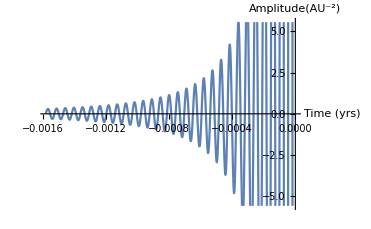

-Graphics-

This plot shows the unmodified GR wave form for R.  The units of R are one over length squared where we are using Astronomical Units to measure length AU^-2 .   Take note of the time scale which is measured in years.  The negative time means time before the inspiral is complete.

This is the waveform for the scalar field ϕ.  Here it is being measured in the same units as R.  However note the time scale on this graph.  The divisions are two orders of magnitude smaller.

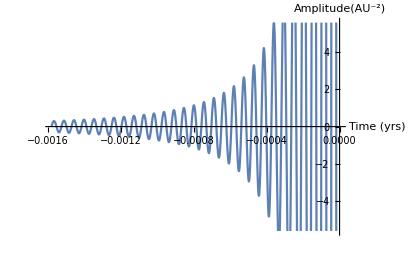

This is the waveform for the scalar field ϕ.  Here it is being measured in the same units as R.  However note the time scale on this graph.  The divisions are two orders of magnitude smaller.

### Plots of the trace of h^μν

This is a plot of the metric waveform, with modifications active. This is the quantity that LISA would directly observe.  Compare this graph to the graph of R above.  Note the time scales are the same but the amplitudes are very different.  Large changes in the amplitude of h make little difference to the amplitude of R.   Conversely large changes in the metric perturbation lead to comparatively small changes in curvature.

-Graphics-

This is a plot of the metric waveform, with modifications active. This is the quantity that LISA would directly observe.

This is a plot of the percent difference in metric waveform from pure GR and the modified theory as a function of time.  This shows that this modified model predicts  the same behavior as GR far from the time of merger but will differ from it by a tiny percentage just before the merger.   The ring down phase of the merger is where we would need to look for these differences.

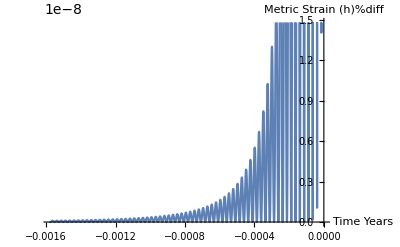

The percent difference in the metric waves as a function of distance at intergalactic scale shows us that the variation from GR is not great and approaches GR as distance increases.

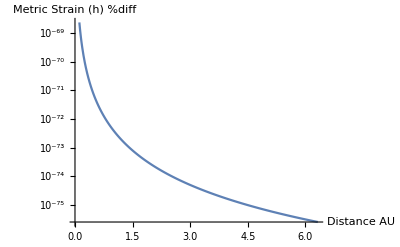

The percent difference in the metric waves as a function of distance at intergalactic scale.   Every multiple of 10^14 AU is 1.58 billion ly, or 484.8 Mpc .

This is a plot of the percent difference in the metric strain with the modifications as a function of distance at solar system scale. Take special note of the size of the percent differences and the sharp peaks that appear.  These sharp peaks are points where the ratio taken as part of the percent difference leads to points which get close to being undefined.  They are not physical singular points but artefacts of this percent difference analysis.

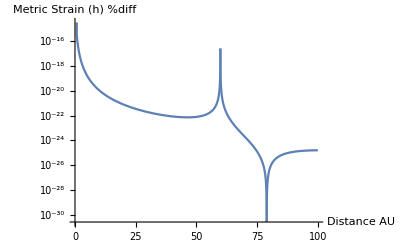

This is a plot of the percent difference in the metric strain with the modifications as a function of distance at solar system scale.

### Plots relating to the stress energy invariant T.

This graph is a plot of the stress energy invariant without any modifications.

-Graphics-

This graph is a plot of the stress energy invariant without any modifications.

This graph is a plot of the stress energy invariant with all modifications active.

-Graphics-

This graph is a plot of the stress energy invariant with all modifications active.

Comparing these two graphs the most notable difference is that with the modifications active the vertical scale maxes out one order of magnitude higher.  This would indicate that a large quantity of energy is being pumped into the scalar field and the interaction between the scalar field and the gravitational filed.  Given that the scalar field is intended to be dark matter it would be sensible if the effect it had on the energy invariant was large.

The percentage differences in the energies are small at all distances.  This means we can rule out dramatic differences in the trajectories of objects.

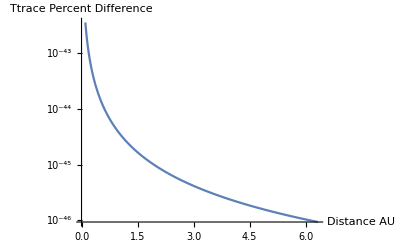

The same graph as the above but zooming in at solar system scale.

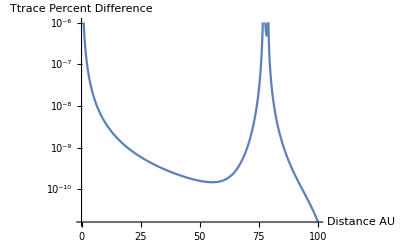

#### Plots relating to the integrated stress energy invariant ∫TⅆR

The curvature integrated stress energies,∫TⅆR, show a cumulative effect of those tiny differences. On the galactic cluster scale of the next graph the result is a large departure from GR.  Given that the scalar field ϕ is meant to be the dark matter (and possibly also a form of dark energy)

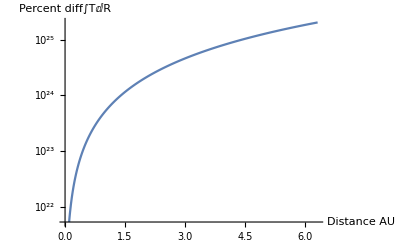

Next we look at a plot of the same quantity at solar system scale. The percentage difference is tiny, even near the singular points in this computation which are not physical.

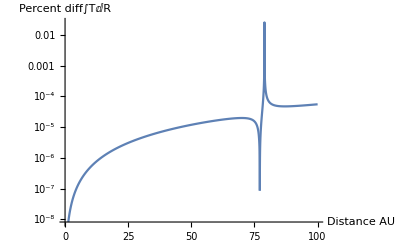

## Discussion.

Let us return our attention to the graph of percent difference in metric strain vs distance in AU.  As the in spiraling EMRI approaches the percent difference from the GR prediction will be on the order of 10^-18%.

-Graphics-

LISA will have 10^-20strain resolution16-17.  This of course depends on frequency   Unless I am misunderstanding that would mean it could distinguish a percent difference of  10^-18%.  While the in spiraling object is at solar system distances from the black hole it is spiraling towards LISA may be able to detect effects due to the modified theory.

Looking even closer we see that at a distance from the black hole that corresponds to the radius of the event horizon, we get a percent difference of about 10^-13% or 10^-15.  The signal of these differences from GR should be biggest when the gravitational waves are of greatest amplitude in the instants just before merger.

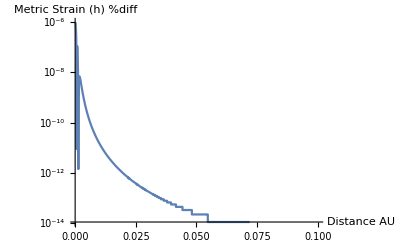

Looking even closer we see that at a distance from the black hole that corresponds to the radius of the event horizon, we get a percent difference of about 10^-13% or 10^-15.

From the perspective of detecting the effects of this model with LISA there is a good chance it will.

### The values of the parameters.

A still open question is what should the values of the parameters which appear in this theory.  We presumed them to be small numbers.  The analyses in this paper point towards values for the parameters.  ξ has a maximum value around 6.22969×10^-20 and β to no more than 1/5000000000 AU^2. Larger values than these lead to differences from General Relativity which are too large.  These are empirical values and seem to bear no relation to any previously known fundamental constants.  That said β being a rational number is intriguing.   If it is multiplied by the cosmological constant the result is a dimensionless value of exactly 5×10^-40.

### LISA FP WG Views on Testing Such Theories.

In two papers the FP WG has expounded on how to test such models. 13 14  The model in this work is a combination of Quadratic gravity with a massive scalar field.  They propose testing these in a PPE framework. 15  That method will certainly have many advantages over the approach taken in this paper.  While this paper presents an exact solution, it is not of simple form.

To take its’ derivatives and integrals is not simple.  That said, working with these exact solutions, which can be Taylor expanded to get series that allow approximation to any desired precision.

## References

Starobinskii AA (1979),"Spectrum of relict gravitational radiation and the early state of the universe",ZhETF Pisma Redaktsiiu.,December,1979. Vol.30,pp.719-723.  https://ui.adsabs.harvard.edu/abs/1979ZhPmR..30..719S/abstract  Starobinsky AA (1980), “A new type of isotropic cosmological models without singularity”, Physics Letters B., March, 1980. Vol. 91(1), pp. 99-102. https://doi.org/10.1016/0370-2693(80)90670-X

Hu W, Barkana R and Gruzinov A (2000), "Fuzzy Cold Dark Matter: The Wave Properties of Ultralight Particles", Physical Review Letters., August, 2000. Vol. 85(6), pp. 1158-1161.  https://doi.org/10.1103/PhysRevLett.85.1158

Duffy LD and van Bibber K (2009), "Axions as dark matter particles", New Journal of Physics., October, 2009. Vol. 11(10), pp. 105008.
https://doi.org/10.1088/1367-2630/11/10/105008.

Pravda V, Pravdová A, Podolský J and Švarc R (2017), “Exact solutions to quadratic gravity”, Physical Review D., April, 2017. Vol. 95(8), pp. 084025. https://doi.org/10.1103/PhysRevD.95.084025

Cornish N, Sampson L, Yunes N and Pretorius F (2011), "Gravitational wave tests of general relativity with the parameterized post-Einsteinian framework", Physical Review D., September, 2011. Vol. 84(6), pp. 062003 https://doi.org/10.1103/PhysRevD.84.062003

Katz ML, Chua AJK, Speri L, Warburton N and Hughes SA (2021), “Fast extreme-mass-ratio-inspiral waveforms: New tools for millihertz gravitational-wave data analysis”, Physical Review D., September, 2021. Vol. 104(6), pp. 064047. https://doi.org/10.1103/PhysRevD.104.064047

Geng CQ (2012), “Gravitational Waves in Viable Modified Gravity Theories”, In Journal of Physics Conference Series., September, 2012. Vol. 384, pp. 012030.  https://doi.org/10.1088/1742-6596/384/1/012030

Gourgoulhon E, Le Tiec A, Vincent FH and Warburton N (2019), “Gravitational waves from bodies orbiting the Galactic center black hole and their detectability by LISA”, Astronomy and Astrophysics., July, 2019. Vol. 627, pp. A92. https://doi.org/10.1051/0004-6361/201935406

Park RS, Folkner WM, Konopliv AS, Williams JG, Smith DE and Zuber MT (2017), “Precession of Mercury’s Perihelion from Ranging to the MESSENGER Spacecraft”, The Astronomical Journal., March, 2017. Vol. 153(3), pp. 121. https://doi.org/10.3847/1538-3881/aa5be2

Clemence GM (1947), “The Relativity Effect in Planetary Motions”, Reviews of Modern Physics., October, 1947. Vol. 19(4), pp. 361-364. https://doi.org/10.1103/RevModPhys.19.361

Fomalont E, Kopeikin S, Lanyi G and Benson J (2009), “Progress in Measurements of the Gravitational Bending of Radio Waves Using the VLBA”, The Astrophysical Journal., July, 2009. Vol. 699(2), pp. 1395-1402. https://doi.org/10.1088/0004-637X/699/2/1395

Arun KG, Belgacem E, Benkel R, Bernard L, Berti E, Bertone G, Besancon M, Blas D, Böhmer CG, Brito R, Calcagni G, Cardenas-Avendaño A, Clough K, Crisostomi M, De Luca V, Doneva D, Escoffier S, Ezquiaga JM, Ferreira PG, Fleury P, Foffa S, Franciolini G, Frusciante N, Garc\ia-Bellido J, Herdeiro C, Hertog T, Hinderer T, Jetzer P, Lombriser L, Maggio E, Maggiore M, Mancarella M, Maselli A, Nampalliwar S, Nichols D, Okounkova M, Pani P, Paschalidis V, Raccanelli A, Randall L, Renaux-Petel S, Riotto A, Ruiz M, Saffer A, Sakellariadou M, Saltas ID, Sathyaprakash BS, Shao L, Sopuerta CF, Sotiriou TP, Stergioulas N, Tamanini N, Vernizzi F, Witek H, Wu K, Yagi K, Yazadjiev S, Yunes N, Zilhao M, Afshordi N, Angonin M-C, Baibhav V, Barausse E, Barreiro T, Bartolo N, Bellomo N, Ben-Dayan I, Bergshoeff EA, Bernuzzi S, Bertacca D, Bhagwat S, Bonga B, Burko LM, Compere G, Cusin G, da Silva A, Das S, de Rham C, Destounis K, Dimastrogiovanni E, Duque F, Easther R, Farmer H, Fasiello M, Fisenko S, Fransen K, Frauendiener J, Gair J, Arpad Gergely L, Gerosa D, Gualtieri L, Han W-B, Hees A, Helfer T, Hennig J, Jenkins AC, Kajfasz E, Kaloper N, Karas V, Kavanagh BJ, Klioner SA, Koushiappas SM, Lagos M, Le Poncin-Lafitte C, Lobo FSN, Markakis C, Martin-Moruno P, Martins CJAP, Matarrese S, Mayerson DR, Mimoso JP, Noller J, Nunes NJ, Oliveri R, Orlando G, Pappas G, Pikovski I, Pilo L, Podolsky J, Pratten G, Prokopec T, Qi H, Rastgoo S, Ricciardone A, Rollo R, Rubiera-Garcia D, Sergijenko O, Shapiro S, Shoemaker D, Spallicci A, Stashko O, Stein LC, Tasinato G, Tolley AJ, Vagenas EC, Vandoren S, Vernieri D, Vicente R, Wiseman T, Zhdanov VI and Zumalacárregui M (2022), “New Horizons for Fundamental Physics with LISA”, arXiv e-prints., May, 2022. , pp. arXiv:2205.01597. https://ui.adsabs.harvard.edu/abs/2022arXiv220501597A

Barausse E, Berti E, Hertog T, Hughes SA, Jetzer P, Pani P, Sotiriou TP, Tamanini N, Witek H, Yagi K, Yunes N, Abdelsalhin T, Achucarro A, van Aelst K, Afshordi N, Akcay S, Annulli L, Arun KG, Ayuso I, Baibhav V, Baker T, Bantilan H, Barreiro T, Barrera-Hinojosa C, Bartolo N, Baumann D, Belgacem E, Bellini E, Bellomo N, Ben-Dayan I, Bena I, Benkel R, Bergshoefs E, Bernard L, Bernuzzi S, Bertacca D, Besancon M, Beutler F, Beyer F, Bhagwat S, Bicak J, Biondini S, Bize S, Blas D, Boehmer C, Boller K, Bonga B, Bonvin C, Bosso P, Bozzola G, Brax P, Breitbach M, Brito R, Bruni M, Brügmann B, Bulten H, Buonanno A, Burko LM, Burrage C, Cabral F, Calcagni G, Caprini C, Cárdenas-Avendaño A, Celoria M, Chatziioannou K, Chernoff D, Clough K, Coates A, Comelli D, Compère G, Croon D, Cruces D, Cusin G, Dalang C, Danielsson U, Das S, Datta S, de Boer J, De Luca V, De Rham C, Desjacques V, Destounis K, Di Filippo F, Dima A, Dimastrogiovanni E, Dolan S, Doneva D, Duque F, Durrer R, East W, Easther R, Elley M, Ellis JR, Emparan R, Ezquiaga JM, Fairbairn M, Fairhurst S, Farmer HF, Fasiello MR, Ferrari V, Ferreira PG, Ficarra G, Figueras P, Fisenko S, Foffa S, Franchini N, Franciolini G, Fransen K, Frauendiener J, Frusciante N, Fujita R, Gair J, Ganz A, Garcia P, Garcia-Bellido J, Garriga J, Geiger R, Geng C, Gergely LÁ, Germani C, Gerosa D, Giddings SB, Gourgoulhon E, Grandclement P, Graziani L, Gualtieri L, Haggard D, Haino S, Halburd R, Han WB, Hawken AJ, Hees A, Heng IS, Hennig J, Herdeiro C, Hervik S, Holten Jv, Hoyle CD, Hu Y, Hull M, Ikeda T, Isi M, Jenkins A, Julié F, Kajfasz E, Kalaghatgi C, Kaloper N, Kamionkowski M, Karas V, Kastha S, Keresztes Z, Kidder L, Kimpson T, Klein A, Klioner S, Kokkotas K, Kolesova H, Kolkowitz S, Kopp J, Koyama K, Krishnendu NV, Kroon JAV, Kunz M, Lahav O, Landragin A, Lang RN, Le Poncin-Lafitte C, Lemos J, Li B, Liberati S, Liguori M, Lin F, Liu G, Lobo FSN, Loll R, Lombriser L, Lovelace G, Macedo RP, Madge E, Maggio E, Maggiore M, Marassi S, Marcoccia P, Markakis C, Martens W, Martinovic K, Martins CJAP, Maselli A, Mastrogiovanni S, Matarrese S, Matas A, Mavromatos NE, Mazumdar A, Meerburg PD, Megias E, Miller J, Mimoso JP, Mittnacht L, Montero MM, Moore B, Martin-Moruno P, Musco I, Nakano H, Nampalliwar S, Nardini G, Nielsen A, Novák J, Nunes NJ, Okounkova M, Oliveri R, Oppizzi F, Orlando G, Oshita N, Pappas G, Paschalidis V, Peiris H, Peloso M, Perkins S, Pettorino V, Pikovski I, Pilo L, Podolsky J, Pontzen A, Prabhat S, Pratten G, Prokopec T, Prouza M, Qi H, Raccanelli A, Rajantie A, Randall L, Raposo G, Raymond V, Renaux-Petel S, Ricciardone A, Riotto A, Robson T, Roest D, Rollo R, Rosofsky S, Ruan JJ, Rubiera-Garc\ia D, Ruiz M, Rusu M, Sabatie F, Sago N, Sakellariadou M, Saltas ID, Sberna L, Sathyaprakash B, Scheel M, Schmidt P, Schutz B, Schwaller P, Shao L, Shapiro SL, Shoemaker D, Silva Ad, Simpson C, Sopuerta CF, Spallicci A, Stefanek BA, Stein L, Stergioulas N, Stott M, Sutton P, Svarc R, Tagoshi H, Tahamtan T, Takeda H, Tanaka T, Tantilian G, Tasinato G, Tattersall O, Teukolsky S, Tiec AL, Theureau G, Trodden M, Tolley A, Toubiana A, Traykova D, Tsokaros A, Unal C, Unnikrishnan CS, Vagenas EC, Valageas P, Vallisneri M, Van den Brand J, Van den Broeck C, van de Meent M, Vanhove P, Varma V, Veitch J, Vercnocke B, Verde L, Vernieri D, Vernizzi F, Vicente R, Vidotto F, Visser M, Vlah Z, Vretinaris S, Völkel S, Wang Q, Wang Y-T, Werner MC, Westernacher J, Weygaert Rvd, Wiltshire D, Wiseman T, Wolf P, Wu K, Yamada K, Yang H, Yi L, Yue X, Yvon D, Zilhão M, Zimmerman A and Zumalacarregui M (2020), “Prospects for fundamental physics with LISA”, General Relativity and Gravitation., August, 2020. Vol. 52(8), pp. 81. https://doi.org/10.1007/s10714-020-02691-1

Loutrel N, Yunes N and Pretorius F (2014), “Parametrized post-Einsteinian framework for gravitational wave bursts”, Physical Review D., November, 2014. Vol. 90(10), pp. 104010.  https://doi.org/10.1103/PhysRevD.90.104010

Robson T, Cornish NJ and Liu C (2019), “The construction and use of LISA sensitivity curves”, Classical and Quantum Gravity., May, 2019. Vol. 36(10), pp. 105011. https://doi.org/10.1088/1361-6382/ab1101